```mathematica
(* Mathematica code for Model3 of Eshra et al. eLife 2021 *)
(* Stefan Hallermann and Hartmut Schmidt Aug 2021 *)
```

# Import

## general

```mathematica
(* imported data all Ca in uM, all times in ms, all ampltiudes and Nv in vesicels *)
```

```mathematica
CmToVesConversionFactor = (1/90.12)*(1/70*^-18);(* explained in methods *)
```

```mathematica
rrp=10;(* pool of release-ready vesicles per connection *)
```

```mathematica
dir=NotebookDirectory[];
SetDirectory[dir]; 
dataFolder="../data to fit/";
```

## tau1 Cm 5kHz

```mathematica
data=Import[dataFolder<>"all_t1_v02_C5.txt","Table"];
```

```mathematica
dataT1C5Ca=0.001*data[[All,1]];
dataT1C5RelRate=1000.*data[[All,2]];
dataT1C5Delay=data[[All,3]];
dataT1C5ChiRatio= data[[All,4]];
dataT1C5Amplitude=CmToVesConversionFactor data[[All,5]];

dataT1C5Nv=Table[0,{7}];
tmp1=1;tmp2=6;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
```

## tau1 Cm 10kHz

```mathematica
data=Import[dataFolder<>"all_t1_v02_C10.txt","Table"];
```

```mathematica
dataT1C10Ca=0.001*data[[All,1]];
dataT1C10RelRate=1000.*data[[All,2]];
dataT1C10Delay=data[[All,3]];
dataT1C10ChiRatio= data[[All,4]];
dataT1C10Amplitude=CmToVesConversionFactor data[[All,5]];

dataT1C10Nv=Table[0,{7}];
tmp1=1;tmp2=6;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
```

## tau1 Deconv

```mathematica
data=Import[dataFolder<>"all_t1_v02_D.txt","Table"];
```

```mathematica
dataT1DCa=0.001*data[[All,1]];
dataT1DRelRate=1000.*data[[All,2]];
dataT1DDelay=data[[All,3]];
dataT1DChiRatio= data[[All,4]];
dataT1DAmplitude= data[[All,5]];

dataT1DNv=Table[0,{7}];
tmp1=1;tmp2=6;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
```

## tau2 Cm 5kHz

```mathematica
data=Import[dataFolder<>"all_t2_v02_C5.txt","Table"];
```

```mathematica
dataT2C5Ca=0.001*data[[All,1]];
dataT2C5RelRate=1000.*data[[All,2]];
dataT2C5Amplitude2=CmToVesConversionFactor data[[All,3]];
dataT2C5Amplitude1=CmToVesConversionFactor data[[All,4]];
```

## tau2 Cm 10kHz

```mathematica
data=Import[dataFolder<>"all_t2_v02_C10.txt","Table"];
```

```mathematica
dataT2C10Ca=0.001*data[[All,1]];
dataT2C10RelRate=1000.*data[[All,2]];
dataT2C10Amplitude2=CmToVesConversionFactor data[[All,3]];dataT2C10Amplitude1=CmToVesConversionFactor data[[All,4]];
```

## tau2 Deconv

```mathematica
data=Import[dataFolder<>"all_t2_v02_D.txt","Table"];
```

```mathematica
dataT2DCa=0.001*data[[All,1]];
dataT2DRelRate=1000.*data[[All,2]];
dataT2DAmplitude2= data[[All,3]];
dataT2DAmplitude1= data[[All,4]];
```

## local Ca

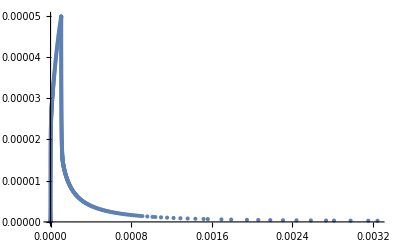

```mathematica
data=Import[dataFolder<>"local Ca at 20 nm in uM and ms.txt","Table"];
dataLocalCa=1*^-6 data[[All,1]];
dataLocalCaTime=1*^-3 data[[All,2]];
ListPlot[Transpose[{dataLocalCaTime,dataLocalCa}],PlotRange->All]
```

# General parameters and definitions

## general stuff

```mathematica
(* for calulations: time in s, Ca in M *)
numberOfFitParamToBeSaved=16;
(*
1 max release

Mono
2 chi2Mono
3 delayMono
4 ampMono
5 1/tau1Mono

Bi
6 chi2Mono/chi2Bi
7 delay
8 amp
9 amp1 (=amp*relative amp1)
10 1/tau1
11 1/tau2

merge
12 delay
13 amp
14 amp1
15 1/tau1
16 1/tau2
*)
cursorStart=-0.002;(*s*)
cursorEnd=0.01;(*s*)
cursorEndLong=0.061;(*s*)
timeOfNv={0.0001,0.0002,0.001,0.005,0.01,0.1,0.4};
SeedRandom[1];
myMaxIterations=100;
```

```mathematica
timeStart=AbsoluteTime[]
```

3.841510544996684×10^9

## noiseRepeats

```mathematica
noiseRepeats=3;
(* should be increased to 50 for a full dataset *)
myQuantile1=0.25;
myQuantile2=0.75;
```

## export parameters

```mathematica
dtOfPlotsForExport=20*^-5;
exportYes=1;
```

## sampling and myNoise

```mathematica
samplingOfDataInKHzC5=5;
myNoiseC5=CmToVesConversionFactor*1.36937*^-14/rrp(*cannot be 0*)
signalToNoiseRatioC5=1.;(*minimum s-to-n-ratio to attempt fitting*)
dtOfDataC5=(1/(1000*samplingOfDataInKHzC5));

samplingOfDataInKHzC10=10;
myNoiseC10=CmToVesConversionFactor*1.67583*^-14/rrp(*cannot be 0*)
signalToNoiseRatioC10=1.;(*minimum s-to-n-ratio to attempt fitting*)
dtOfDataC10=(1/(1000*samplingOfDataInKHzC10));

samplingOfDataInKHzD=10;
myNoiseD=0.367584/rrp(*cannot be 0*)
signalToNoiseRatioD=1.;(*minimum s-to-n-ratio to attempt fitting*)
dtOfDataD=(1/(1000*samplingOfDataInKHzD));

samplingOfDataInKHzLong=1;
myNoiseLong=myNoiseC5;(*cannot be 0*)
dtOfDataLong=(1/(1000*samplingOfDataInKHzLong));
```

0.217071

0.265651

0.0367584

## number of simulations per DMN

```mathematica
aNumberDMN05=2;
aNumberDMN2=2;
aNumberDMN10=2;

(* for full dataset: *)
(*
aNumberDMN05=2*20;
aNumberDMN2=2*17;
aNumberDMN10=2*10;
*)
```

## Exp fit function

```mathematica
myFitMono[t_]:=If[t<=delayMono,0,ampMono (1- Exp[-(t-delayMono)/tau1Mono])];

myFitBi[t_]:=If[t<=delay,0,amp (1- amp1 Exp[-(t-delay)/tau1]-(1-amp1) Exp[-(t-delay)/tau2])];

(*guess for 10 uM; will be changed according to a power of 1 law*)(*in s*)
ampGuess=2.;(*each pool has size 1.0*)
tau1Guess=0.001;(*in s*)
delayGuess=0.0005;(*in s*)
amp1Guess=0.5;
```

```mathematica
pre_final01
```

pre_final01

# Calculate Ca transients

#### First, the resting conditions are numerically calculated. Subsequently, the resulting values are used as initial conditions for the main simulations of the flash-evoked Ca2+ transitions . All calculations are repeated in a loop with increasing uncaging efficacy for three different DMN concentrations. The resulting free Ca2+ concentration is later used to drive the release schemes.

## General definitions for all DMN conc.

```mathematica
CaListReal=CaListDye={};
```

## 0.5 mM DMN

## general parameters

```mathematica
TimeWindow=0.006; (*End of simulation*)
tflash=0.0;   (*Time of flash*)
PlStart=0.; (*Plot start*)

af=0.67; (*fast uncaging fraction; Faas et al*)

(*Select dye*)
OGB1=0;
OGB5N=0;
OGB6F=0;
Fluo5F=1;

CaRest=227.*10^-9; (*Free pre-flash rersting Ca; equilibrates with all buffers and DM*)
MgT=0.5*10^-3; (*total Mg in pipette*)
γ=0.;  (*Pump rate*)

(*Concentrations of dye, buffers, DM*)
OGtotal =50.*10^-6 ;
ATPtotal =5.*10^-3 ;
MBtotal =480.*10^-6 ;(*(*Delvendahl, PNAS, 2015*)*)   

DMT = 0.5*10^-3;    (*total concentration of DMn *)
(*uncaging efficiency*)
aStartDMN05=0.08;
aEndDMN05=0.5;
```

## definitions and loop

```mathematica
(*Dye*)
If[OGB1==1,
kOnOG  = 4.3*10^8;
kOffOG = 103.;]

If[OGB5N==1,
kOnOG  = 2.5*10^8;
kOffOG = 6000.*31.4/24;]

If[OGB6F==1,
kOnOG  = 3.*10^8;
kOffOG = 900.;]

If[Fluo5F==1,
kOnOG  = 3.*10^8;
kOffOG = 249.;] (*Delvendahl PNAS; before: 432*)

KdOG = kOffOG/kOnOG;
kappaOG=OGtotal/KdOG;

(*ATP*)
kOnATP  = 5.*10^8;
kOffATP = 100000.;
kOnMgATP  = 1.*10^7; (*Bollmann Dissertation S. 59; *)
kOffMgATP = 1000.;

KdATP = kOffATP/kOnATP;
kappaATP=ATPtotal/KdATP;
KdMgATP = kOffMgATP/kOnMgATP;

(*DM*)
If[MgT==0.,
kOnDM=1.98*10^7;(*Faas Plos Biol, 2007*)
kOffDM = 0.14;  
,
kOnDM=2.9*10^7;(*Faas Biophys J, 2005*)
kOffDM = 0.19;
]

(*Mg binding constants for DMn, DMf, DMs*)
kOnMg=1.3*10^5;  (*all values for Mg are from Faas et al., 2005*)
kOffMg=0.2;

(*Ca binding constants for PP*)
kOnPP2=kOnPP1=kOnDM;
kOffPP2=3.6*10^3;
If[MgT==0.,
kOffPP1=7.*10^4;,
kOffPP1=6.9*10^4;  ]

(*Mg binding constants for PP1,PP2*)
kOffMgPP=3.*10^2; (*for PP1,PP2*)
konMgPP=kOnMg; (*koMgPP not used in below diff. eq., only kOnMg*)

(*Equilibrium constants (not complete)*)
KdDM = kOffDM/kOnDM;
KdPP1=kOffPP1/kOnPP1;
KdMg = kOffMg/kOnMg;
kappaDM=DMT/KdDM;

 (*Endogenous buffer*)
kOnMB  = 5*10^8;(*Delvendahl, PNAS, 2015*)
kOffMB =16000;
KdMB = kOffMB/kOnMB;

TRest=1000.;


(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)


For[aCount=1,aCount≤ aNumberDMN05,aCount+=1,
a=10^(Log10[aStartDMN05]+(aCount-1)*(Log10[aEndDMN05]-Log10[aStartDMN05])/(aNumberDMN05-1));

(*------------------------- Resting Equations -------------------------------------------*)

(*Dye*)
OGRest:={

OG[0]==OGtotal,
CaOG[0]==0,

OG'[tt]==-kOnOG*CaRest* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*CaRest* OG[tt]- kOffOG *CaOG[tt]
}
;

(*ATP*)
ATPRest:={

ATP[0]==ATPtotal,
CaATP[0]==0,
MgATP[0]==0,

ATP'[tt]==-kOnATP*CaRest* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*CaRest* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]

}

;

(*DM nitrophene*)
DMnRest:={

DMn[0]==(1-a)*DMT,
CaDMn[0]==0.,
MgDMn[0]==0.,

DMn'[tt]==-kOnDM*CaRest* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*CaRest* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}

;
DMfRest:={

DMf[0]==a*af*DMT,
CaDMf[0]==0.,
MgDMf[0]==0.,

DMf'[tt]==-kOnDM*CaRest* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt],
CaDMf'[tt]==kOnDM*CaRest* DMf[tt]- kOffDM *CaDMf[tt],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]
}

;
DMsRest:={

DMs[0]==a*(1-af)*DMT,
CaDMs[0]==0.,
MgDMs[0]==0.,

DMs'[tt]==-kOnDM*CaRest* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt],
CaDMs'[tt]==kOnDM*CaRest* DMs[tt]- kOffDM *CaDMs[tt],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]
}
;

(*Endogeneous buffer*)
MBRest:={

MB[0]==MBtotal,
CaMB[0]==0,

MB'[tt]==-kOnMB*CaRest* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*CaRest*MB[tt]- kOffMB *CaMB[tt]
}

;

(*Free Mg*)
MgfRest:={
Mg[0]==MgT,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
}

;
EqRest:={ATPRest,MgfRest,OGRest,DMnRest,DMfRest,DMsRest,MBRest};
VarsRest:={ATP,Mg,CaATP,MgATP,CaOG,OG,DMn,CaDMn,MgDMn,DMf,CaDMf,MgDMf,DMs,CaDMs,MgDMs,MB,CaMB}
;
solr:=NDSolve[EqRest,VarsRest,{tt,0,TRest}]
;

Ca0 =CaRest;
Mg0 = Extract[Mg[TRest]/.solr,1];
ATP0 = Extract[ATP[TRest]/.solr,1];
CaATP0=Extract[CaATP[TRest]/.solr,1];
MgATP0=Extract[MgATP[TRest]/.solr,1];
OG0 = Extract[OG[TRest]/.solr,1];
CaOG0 = Extract[CaOG[TRest]/.solr,1];
DMn0= Extract[DMn[TRest]/.solr,1];
CaDMn0= Extract[CaDMn[TRest]/.solr,1];
MgDMn0= Extract[MgDMn[TRest]/.solr,1];
DMf0= Extract[DMf[TRest]/.solr,1];
CaDMf0= Extract[CaDMf[TRest]/.solr,1];
MgDMf0= Extract[MgDMf[TRest]/.solr,1];
DMs0= Extract[DMs[TRest]/.solr,1];
CaDMs0= Extract[CaDMs[TRest]/.solr,1];
MgDMs0= Extract[MgDMs[TRest]/.solr,1];
MB0 = Extract[MB[TRest]/.solr,1];
CaMB0 = Extract[CaMB[TRest]/.solr,1];


ClearAll[EqRest,VarsRest];


(*------------------------- Flash Equations -------------------------------------------*)

(*Dye*)
BufferOG:={

OG[0]==OG0,
CaOG[0]==CaOG0,

OG'[tt]==-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*Ca[tt]* OG[tt]- kOffOG *CaOG[tt]}
;

(*ATP*)
BufferATP:={

ATP[0]==ATP0,
CaATP[0]==CaATP0,
MgATP[0]==MgATP0,

ATP'[tt]==-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*Ca[tt]* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]
}
;

(*fast (tauf) and slow (taus) time constants for uncageing; Faas et al., 2005,2007*)
If[MgT==0.,
tauf=15.2*10^-6;  (*Faas, 2007*)
taus=1.9*10^-3;  
,
tauf=15.*10^-6;  (*Faas,2005*)
taus=2.*10^-3;  ]

;

(*The differential equations*)
(*non uncaging fraction of DMn*)
BufferDMn:={

DMn[0]==DMn0,
CaDMn[0]==CaDMn0,
MgDMn[0]==MgDMn0,

DMn'[tt]==-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*Ca[tt]* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}
;

(*fast uncaging fraction of DMn*)
BufferDMf:={

DMf[0]==DMf0,
CaDMf[0]==CaDMf0,
MgDMf[0]==MgDMf0,

DMf'[tt]==-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]-1/tauf*DMf[tt]*UnitStep[tt-tflash],
CaDMf'[tt]==kOnDM*Ca[tt]* DMf[tt]- kOffDM *CaDMf[tt]-1/tauf*CaDMf[tt]*UnitStep[tt-tflash],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]-1/tauf*MgDMf[tt]*UnitStep[tt-tflash]
}

;
(*slow uncaging fraction of DMn*)
BufferDMs:={

DMs[0]==DMs0,
CaDMs[0]==CaDMs0,
MgDMs[0]==MgDMs0,

DMs'[tt]==-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]-1/taus*DMs[tt]*UnitStep[tt-tflash],
CaDMs'[tt]==kOnDM*Ca[tt]* DMs[tt]- kOffDM *CaDMs[tt]-1/taus*CaDMs[tt]*UnitStep[tt-tflash],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]-1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*Photoproducts*)
(*PP2: comes from DMf,DMs and MgDMf,MgDMs; but also binds Ca*)
BufferPP2:={

PP2[0]==0,
CaPP2[0]==0,
MgPP2[0]==0,

PP2'[tt]==-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]+2*(1/tauf*DMf[tt]*UnitStep[tt-tflash]+1/taus*DMs[tt]*UnitStep[tt-tflash])
+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash],

CaPP2'[tt]==kOnPP2*Ca[tt]* PP2[tt]- kOffPP2*CaPP2[tt],

MgPP2'[tt]==kOnMg*Mg[tt]* PP2[tt]- kOffMgPP*MgPP2[tt]+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*PP1: Comes from CaDMf,CaDMs and binds Ca and Mg*)
BufferPP1:={

PP1[0]==0,
CaPP1[0]==0,
MgPP1[0]==0,

PP1'[tt]==-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

CaPP1'[tt]==kOnPP1*Ca[tt]* PP1[tt]- kOffPP1 *CaPP1[tt]+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

MgPP1'[tt]==kOnMg*Mg[tt]* PP1[tt]- kOffMgPP*MgPP1[tt]

}
;

(*Endogeneous Buffer*)
BufferMB:={

MB[0]==MB0,
CaMB[0]==CaMB0,

MB'[tt]==-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*Ca[tt]*MB[tt]- kOffMB *CaMB[tt]}

;

(*Clear[Eqns,Vars,sol]*)

(*Free Ca*)
FreeCa:= {
Ca[0]==Ca0,

Ca'[tt]== -γ *(Ca[tt]-CaRest)
(*DMn*)
-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]
-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]
-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]
-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]
-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]
(*buffers*)
-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]
-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt]
(*dye*)
-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt]
 }
;

(*Free Mg*)
FreeMg:={
Mg[0]==Mg0,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]
-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
}

;

Eqns:={BufferDMn,BufferDMf,BufferDMs,BufferATP,BufferPP1,BufferPP2,FreeCa,FreeMg,BufferMB,BufferOG}
;
Vars:={ATP,CaATP,MgATP,Ca,Mg,CaDMn,DMn,CaDMf,DMf,CaDMs,DMs,CaPP1,PP1,CaPP2,PP2,MgPP2,MgPP1,MB,CaMB,OG,CaOG}
;
sol := NDSolve[Eqns,Vars,{tt,0.,TimeWindow}(*,Method->{"EquationSimplification"->"Solve"}*)]
;
CafP=Extract[Ca[TimeWindow]/.sol,1];
CafOG=KdOG*CaOG[tt]/OG[tt];

AppendTo[CaListReal,Evaluate[{Ca[tt]}/.sol]];
AppendTo[CaListDye,Evaluate[{CafOG}/.sol]];

];
```

## 2 mM DMN

## general parameters

```mathematica
TimeWindow=0.006; (*End of simulation*)
tflash=0.0;   (*Time of flash*)
PlStart=0.; (*Plot start*)

af=0.67; (*fast uncaging fraction; Faas et al*)

(*Select dye*)
OGB1=0;
OGB5N=1;
OGB6F=0;
Fluo5F=0;

CaRest=227.*10^-9; (*Free pre-flash rersting Ca; equilibrates with all buffers and DM*)
MgT=0.5*10^-3; (*total Mg in pipette*)
γ=0.;  (*Pump rate*)

(*Concentrations of dye, buffers, DM*)
OGtotal =200.*10^-6 ;
ATPtotal =5.*10^-3 ;
MBtotal =480.*10^-6 ;(*(*Delvendahl, PNAS, 2015*)*)   

DMT = 2.*10^-3;    (*total concentration of DMn *)
(*uncaging efficiency*)
aStartDMN2=0.15;
aEndDMN2=0.55;
```

## definitions and loop

```mathematica
(*Dye*)
If[OGB1==1,
kOnOG  = 4.3*10^8;
kOffOG = 103.;]

If[OGB5N==1,
kOnOG  = 2.5*10^8;
kOffOG = 6000.*31.4/24;]

If[OGB6F==1,
kOnOG  = 3.*10^8;
kOffOG = 900.;]

If[Fluo5F==1,
kOnOG  = 3.*10^8;
kOffOG = 249.;] (*Delvendahl PNAS; before: 432*)

KdOG = kOffOG/kOnOG;
kappaOG=OGtotal/KdOG;

(*ATP*)
kOnATP  = 5.*10^8;
kOffATP = 100000.;
kOnMgATP  = 1.*10^7; (*Bollmann Dissertation S. 59; *)
kOffMgATP = 1000.;

KdATP = kOffATP/kOnATP;
kappaATP=ATPtotal/KdATP;
KdMgATP = kOffMgATP/kOnMgATP;

(*DM*)
If[MgT==0.,
kOnDM=1.98*10^7;(*Faas Plos Biol, 2007*)
kOffDM = 0.14;  
,
kOnDM=2.9*10^7;(*Faas Biophys J, 2005*)
kOffDM = 0.19;
]

(*Mg binding constants for DMn, DMf, DMs*)
kOnMg=1.3*10^5;  (*all values for Mg are from Faas et al., 2005*)
kOffMg=0.2;

(*Ca binding constants for PP*)
kOnPP2=kOnPP1=kOnDM;
kOffPP2=3.6*10^3;
If[MgT==0.,
kOffPP1=7.*10^4;,
kOffPP1=6.9*10^4;  ]

(*Mg binding constants for PP1,PP2*)
kOffMgPP=3.*10^2; (*for PP1,PP2*)
konMgPP=kOnMg; (*koMgPP not used in below diff. eq., only kOnMg*)

(*Equilibrium constants (not complete)*)
KdDM = kOffDM/kOnDM;
KdPP1=kOffPP1/kOnPP1;
KdMg = kOffMg/kOnMg;
kappaDM=DMT/KdDM;

 (*Endogenous buffer*)
kOnMB  = 5*10^8;(*Delvendahl, PNAS, 2015*)
kOffMB =16000;
KdMB = kOffMB/kOnMB;

TRest=1000.;


(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)

For[aCount=1,aCount≤ aNumberDMN2,aCount+=1,
a=10^(Log10[aStartDMN2]+(aCount-1)*(Log10[aEndDMN2]-Log10[aStartDMN2])/(aNumberDMN2-1));

(*------------------------- Resting Equations -------------------------------------------*)

(*Dye*)
OGRest:={

OG[0]==OGtotal,
CaOG[0]==0,

OG'[tt]==-kOnOG*CaRest* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*CaRest* OG[tt]- kOffOG *CaOG[tt]
}
;

(*ATP*)
ATPRest:={

ATP[0]==ATPtotal,
CaATP[0]==0,
MgATP[0]==0,

ATP'[tt]==-kOnATP*CaRest* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*CaRest* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]

}

;

(*DM nitrophene*)
DMnRest:={

DMn[0]==(1-a)*DMT,
CaDMn[0]==0.,
MgDMn[0]==0.,

DMn'[tt]==-kOnDM*CaRest* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*CaRest* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}

;
DMfRest:={

DMf[0]==a*af*DMT,
CaDMf[0]==0.,
MgDMf[0]==0.,

DMf'[tt]==-kOnDM*CaRest* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt],
CaDMf'[tt]==kOnDM*CaRest* DMf[tt]- kOffDM *CaDMf[tt],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]
}

;
DMsRest:={

DMs[0]==a*(1-af)*DMT,
CaDMs[0]==0.,
MgDMs[0]==0.,

DMs'[tt]==-kOnDM*CaRest* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt],
CaDMs'[tt]==kOnDM*CaRest* DMs[tt]- kOffDM *CaDMs[tt],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]
}
;

(*Endogeneous buffer*)
MBRest:={

MB[0]==MBtotal,
CaMB[0]==0,

MB'[tt]==-kOnMB*CaRest* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*CaRest*MB[tt]- kOffMB *CaMB[tt]
}

;

(*Free Mg*)
MgfRest:={
Mg[0]==MgT,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
}

;
EqRest:={ATPRest,MgfRest,OGRest,DMnRest,DMfRest,DMsRest,MBRest};
VarsRest:={ATP,Mg,CaATP,MgATP,CaOG,OG,DMn,CaDMn,MgDMn,DMf,CaDMf,MgDMf,DMs,CaDMs,MgDMs,MB,CaMB}
;
solr:=NDSolve[EqRest,VarsRest,{tt,0,TRest}]
;

Ca0 =CaRest;
Mg0 = Extract[Mg[TRest]/.solr,1];
ATP0 = Extract[ATP[TRest]/.solr,1];
CaATP0=Extract[CaATP[TRest]/.solr,1];
MgATP0=Extract[MgATP[TRest]/.solr,1];
OG0 = Extract[OG[TRest]/.solr,1];
CaOG0 = Extract[CaOG[TRest]/.solr,1];
DMn0= Extract[DMn[TRest]/.solr,1];
CaDMn0= Extract[CaDMn[TRest]/.solr,1];
MgDMn0= Extract[MgDMn[TRest]/.solr,1];
DMf0= Extract[DMf[TRest]/.solr,1];
CaDMf0= Extract[CaDMf[TRest]/.solr,1];
MgDMf0= Extract[MgDMf[TRest]/.solr,1];
DMs0= Extract[DMs[TRest]/.solr,1];
CaDMs0= Extract[CaDMs[TRest]/.solr,1];
MgDMs0= Extract[MgDMs[TRest]/.solr,1];
MB0 = Extract[MB[TRest]/.solr,1];
CaMB0 = Extract[CaMB[TRest]/.solr,1];


ClearAll[EqRest,VarsRest];


(*------------------------- Flash Equations -------------------------------------------*)

(*Dye*)
BufferOG:={

OG[0]==OG0,
CaOG[0]==CaOG0,

OG'[tt]==-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*Ca[tt]* OG[tt]- kOffOG *CaOG[tt]}
;

(*ATP*)
BufferATP:={

ATP[0]==ATP0,
CaATP[0]==CaATP0,
MgATP[0]==MgATP0,

ATP'[tt]==-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*Ca[tt]* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]
}
;

(*fast (tauf) and slow (taus) time constants for uncageing; Faas et al., 2005,2007*)
If[MgT==0.,
tauf=15.2*10^-6;  (*Faas, 2007*)
taus=1.9*10^-3;  
,
tauf=15.*10^-6;  (*Faas,2005*)
taus=2.*10^-3;  ]

;

(*The differential equations*)
(*non uncaging fraction of DMn*)
BufferDMn:={

DMn[0]==DMn0,
CaDMn[0]==CaDMn0,
MgDMn[0]==MgDMn0,

DMn'[tt]==-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*Ca[tt]* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}
;

(*fast uncaging fraction of DMn*)
BufferDMf:={

DMf[0]==DMf0,
CaDMf[0]==CaDMf0,
MgDMf[0]==MgDMf0,

DMf'[tt]==-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]-1/tauf*DMf[tt]*UnitStep[tt-tflash],
CaDMf'[tt]==kOnDM*Ca[tt]* DMf[tt]- kOffDM *CaDMf[tt]-1/tauf*CaDMf[tt]*UnitStep[tt-tflash],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]-1/tauf*MgDMf[tt]*UnitStep[tt-tflash]
}

;
(*slow uncaging fraction of DMn*)
BufferDMs:={

DMs[0]==DMs0,
CaDMs[0]==CaDMs0,
MgDMs[0]==MgDMs0,

DMs'[tt]==-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]-1/taus*DMs[tt]*UnitStep[tt-tflash],
CaDMs'[tt]==kOnDM*Ca[tt]* DMs[tt]- kOffDM *CaDMs[tt]-1/taus*CaDMs[tt]*UnitStep[tt-tflash],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]-1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*Photoproducts*)
(*PP2: comes from DMf,DMs and MgDMf,MgDMs; but also binds Ca*)
BufferPP2:={

PP2[0]==0,
CaPP2[0]==0,
MgPP2[0]==0,

PP2'[tt]==-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]+2*(1/tauf*DMf[tt]*UnitStep[tt-tflash]+1/taus*DMs[tt]*UnitStep[tt-tflash])
+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash],

CaPP2'[tt]==kOnPP2*Ca[tt]* PP2[tt]- kOffPP2*CaPP2[tt],

MgPP2'[tt]==kOnMg*Mg[tt]* PP2[tt]- kOffMgPP*MgPP2[tt]+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*PP1: Comes from CaDMf,CaDMs and binds Ca and Mg*)
BufferPP1:={

PP1[0]==0,
CaPP1[0]==0,
MgPP1[0]==0,

PP1'[tt]==-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

CaPP1'[tt]==kOnPP1*Ca[tt]* PP1[tt]- kOffPP1 *CaPP1[tt]+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

MgPP1'[tt]==kOnMg*Mg[tt]* PP1[tt]- kOffMgPP*MgPP1[tt]

}
;

(*Endogeneous Buffer*)
BufferMB:={

MB[0]==MB0,
CaMB[0]==CaMB0,

MB'[tt]==-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*Ca[tt]*MB[tt]- kOffMB *CaMB[tt]}

;

(*Clear[Eqns,Vars,sol]*)

(*Free Ca*)
FreeCa:= {
Ca[0]==Ca0,

Ca'[tt]== -γ *(Ca[tt]-CaRest)
(*DMn*)
-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]
-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]
-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]
-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]
-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]
(*buffers*)
-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]
-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt]
(*dye*)
-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt]
 }
;

(*Free Mg*)
FreeMg:={
Mg[0]==Mg0,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]
-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
}

;

Eqns:={BufferDMn,BufferDMf,BufferDMs,BufferATP,BufferPP1,BufferPP2,FreeCa,FreeMg,BufferMB,BufferOG}
;
Vars:={ATP,CaATP,MgATP,Ca,Mg,CaDMn,DMn,CaDMf,DMf,CaDMs,DMs,CaPP1,PP1,CaPP2,PP2,MgPP2,MgPP1,MB,CaMB,OG,CaOG}
;
sol := NDSolve[Eqns,Vars,{tt,0.,TimeWindow}(*,Method->{"EquationSimplification"->"Solve"}*)]
;
CafP=Extract[Ca[TimeWindow]/.sol,1];
CafOG=KdOG*CaOG[tt]/OG[tt];

AppendTo[CaListReal,Evaluate[{Ca[tt]}/.sol]];
AppendTo[CaListDye,Evaluate[{CafOG}/.sol]];

];
```

## 10 mM DMN

## general parameters

```mathematica
TimeWindow=0.006; (*End of simulation*)
tflash=0.0;   (*Time of flash*)
PlStart=0.; (*Plot start*)

af=0.67; (*fast uncaging fraction; Faas et al*)

(*Select dye*)
OGB1=0;
OGB5N=1;
OGB6F=0;
Fluo5F=0;

CaRest=227.*10^-9; (*Free pre-flash rersting Ca; equilibrates with all buffers and DM*)
MgT=0.5*10^-3; (*total Mg in pipette*)
γ=0.;  (*Pump rate*)

(*Concentrations of dye, buffers, DM*)
OGtotal =200.*10^-6 ;
ATPtotal =5.*10^-3 ;
MBtotal =480.*10^-6 ;(*(*Delvendahl, PNAS, 2015*)*)   

DMT = 10.*10^-3;    (*total concentration of DMn *)
(*uncaging efficiency*)
aStartDMN10=0.14;
aEndDMN10=0.25;
```

## definitions and loop

```mathematica
(*Dye*)
If[OGB1==1,
kOnOG  = 4.3*10^8;
kOffOG = 103.;]

If[OGB5N==1,
kOnOG  = 2.5*10^8;
kOffOG = 6000.*31.4/24;]

If[OGB6F==1,
kOnOG  = 3.*10^8;
kOffOG = 900.;]

If[Fluo5F==1,
kOnOG  = 3.*10^8;
kOffOG = 249.;] (*Delvendahl PNAS; before: 432*)

KdOG = kOffOG/kOnOG;
kappaOG=OGtotal/KdOG;

(*ATP*)
kOnATP  = 5.*10^8;
kOffATP = 100000.;
kOnMgATP  = 1.*10^7; (*Bollmann Dissertation S. 59; *)
kOffMgATP = 1000.;

KdATP = kOffATP/kOnATP;
kappaATP=ATPtotal/KdATP;
KdMgATP = kOffMgATP/kOnMgATP;

(*DM*)
If[MgT==0.,
kOnDM=1.98*10^7;(*Faas Plos Biol, 2007*)
kOffDM = 0.14;  
,
kOnDM=2.9*10^7;(*Faas Biophys J, 2005*)
kOffDM = 0.19;
]

(*Mg binding constants for DMn, DMf, DMs*)
kOnMg=1.3*10^5;  (*all values for Mg are from Faas et al., 2005*)
kOffMg=0.2;

(*Ca binding constants for PP*)
kOnPP2=kOnPP1=kOnDM;
kOffPP2=3.6*10^3;
If[MgT==0.,
kOffPP1=7.*10^4;,
kOffPP1=6.9*10^4;  ]

(*Mg binding constants for PP1,PP2*)
kOffMgPP=3.*10^2; (*for PP1,PP2*)
konMgPP=kOnMg; (*koMgPP not used in below diff. eq., only kOnMg*)

(*Equilibrium constants (not complete)*)
KdDM = kOffDM/kOnDM;
KdPP1=kOffPP1/kOnPP1;
KdMg = kOffMg/kOnMg;
kappaDM=DMT/KdDM;

 (*Endogenous buffer*)
kOnMB  = 5*10^8;(*Delvendahl, PNAS, 2015*)
kOffMB =16000;
KdMB = kOffMB/kOnMB;

TRest=1000.;


(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)

For[aCount=1,aCount≤ aNumberDMN10,aCount+=1,
a=10^(Log10[aStartDMN10]+(aCount-1)*(Log10[aEndDMN10]-Log10[aStartDMN10])/(aNumberDMN10-1));

(*------------------------- Resting Equations -------------------------------------------*)

(*Dye*)
OGRest:={

OG[0]==OGtotal,
CaOG[0]==0,

OG'[tt]==-kOnOG*CaRest* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*CaRest* OG[tt]- kOffOG *CaOG[tt]
}
;

(*ATP*)
ATPRest:={

ATP[0]==ATPtotal,
CaATP[0]==0,
MgATP[0]==0,

ATP'[tt]==-kOnATP*CaRest* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*CaRest* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]

}

;

(*DM nitrophene*)
DMnRest:={

DMn[0]==(1-a)*DMT,
CaDMn[0]==0.,
MgDMn[0]==0.,

DMn'[tt]==-kOnDM*CaRest* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*CaRest* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}

;
DMfRest:={

DMf[0]==a*af*DMT,
CaDMf[0]==0.,
MgDMf[0]==0.,

DMf'[tt]==-kOnDM*CaRest* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt],
CaDMf'[tt]==kOnDM*CaRest* DMf[tt]- kOffDM *CaDMf[tt],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]
}

;
DMsRest:={

DMs[0]==a*(1-af)*DMT,
CaDMs[0]==0.,
MgDMs[0]==0.,

DMs'[tt]==-kOnDM*CaRest* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt],
CaDMs'[tt]==kOnDM*CaRest* DMs[tt]- kOffDM *CaDMs[tt],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]
}
;

(*Endogeneous buffer*)
MBRest:={

MB[0]==MBtotal,
CaMB[0]==0,

MB'[tt]==-kOnMB*CaRest* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*CaRest*MB[tt]- kOffMB *CaMB[tt]
}

;

(*Free Mg*)
MgfRest:={
Mg[0]==MgT,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
}

;
EqRest:={ATPRest,MgfRest,OGRest,DMnRest,DMfRest,DMsRest,MBRest};
VarsRest:={ATP,Mg,CaATP,MgATP,CaOG,OG,DMn,CaDMn,MgDMn,DMf,CaDMf,MgDMf,DMs,CaDMs,MgDMs,MB,CaMB}
;
solr:=NDSolve[EqRest,VarsRest,{tt,0,TRest}]
;

Ca0 =CaRest;
Mg0 = Extract[Mg[TRest]/.solr,1];
ATP0 = Extract[ATP[TRest]/.solr,1];
CaATP0=Extract[CaATP[TRest]/.solr,1];
MgATP0=Extract[MgATP[TRest]/.solr,1];
OG0 = Extract[OG[TRest]/.solr,1];
CaOG0 = Extract[CaOG[TRest]/.solr,1];
DMn0= Extract[DMn[TRest]/.solr,1];
CaDMn0= Extract[CaDMn[TRest]/.solr,1];
MgDMn0= Extract[MgDMn[TRest]/.solr,1];
DMf0= Extract[DMf[TRest]/.solr,1];
CaDMf0= Extract[CaDMf[TRest]/.solr,1];
MgDMf0= Extract[MgDMf[TRest]/.solr,1];
DMs0= Extract[DMs[TRest]/.solr,1];
CaDMs0= Extract[CaDMs[TRest]/.solr,1];
MgDMs0= Extract[MgDMs[TRest]/.solr,1];
MB0 = Extract[MB[TRest]/.solr,1];
CaMB0 = Extract[CaMB[TRest]/.solr,1];


ClearAll[EqRest,VarsRest];


(*------------------------- Flash Equations -------------------------------------------*)

(*Dye*)
BufferOG:={

OG[0]==OG0,
CaOG[0]==CaOG0,

OG'[tt]==-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*Ca[tt]* OG[tt]- kOffOG *CaOG[tt]}
;

(*ATP*)
BufferATP:={

ATP[0]==ATP0,
CaATP[0]==CaATP0,
MgATP[0]==MgATP0,

ATP'[tt]==-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*Ca[tt]* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]
}
;

(*fast (tauf) and slow (taus) time constants for uncageing; Faas et al., 2005,2007*)
If[MgT==0.,
tauf=15.2*10^-6;  (*Faas, 2007*)
taus=1.9*10^-3;  
,
tauf=15.*10^-6;  (*Faas,2005*)
taus=2.*10^-3;  ]

;

(*The differential equations*)
(*non uncaging fraction of DMn*)
BufferDMn:={

DMn[0]==DMn0,
CaDMn[0]==CaDMn0,
MgDMn[0]==MgDMn0,

DMn'[tt]==-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*Ca[tt]* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}
;

(*fast uncaging fraction of DMn*)
BufferDMf:={

DMf[0]==DMf0,
CaDMf[0]==CaDMf0,
MgDMf[0]==MgDMf0,

DMf'[tt]==-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]-1/tauf*DMf[tt]*UnitStep[tt-tflash],
CaDMf'[tt]==kOnDM*Ca[tt]* DMf[tt]- kOffDM *CaDMf[tt]-1/tauf*CaDMf[tt]*UnitStep[tt-tflash],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]-1/tauf*MgDMf[tt]*UnitStep[tt-tflash]
}

;
(*slow uncaging fraction of DMn*)
BufferDMs:={

DMs[0]==DMs0,
CaDMs[0]==CaDMs0,
MgDMs[0]==MgDMs0,

DMs'[tt]==-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]-1/taus*DMs[tt]*UnitStep[tt-tflash],
CaDMs'[tt]==kOnDM*Ca[tt]* DMs[tt]- kOffDM *CaDMs[tt]-1/taus*CaDMs[tt]*UnitStep[tt-tflash],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]-1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*Photoproducts*)
(*PP2: comes from DMf,DMs and MgDMf,MgDMs; but also binds Ca*)
BufferPP2:={

PP2[0]==0,
CaPP2[0]==0,
MgPP2[0]==0,

PP2'[tt]==-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]+2*(1/tauf*DMf[tt]*UnitStep[tt-tflash]+1/taus*DMs[tt]*UnitStep[tt-tflash])
+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash],

CaPP2'[tt]==kOnPP2*Ca[tt]* PP2[tt]- kOffPP2*CaPP2[tt],

MgPP2'[tt]==kOnMg*Mg[tt]* PP2[tt]- kOffMgPP*MgPP2[tt]+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*PP1: Comes from CaDMf,CaDMs and binds Ca and Mg*)
BufferPP1:={

PP1[0]==0,
CaPP1[0]==0,
MgPP1[0]==0,

PP1'[tt]==-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

CaPP1'[tt]==kOnPP1*Ca[tt]* PP1[tt]- kOffPP1 *CaPP1[tt]+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

MgPP1'[tt]==kOnMg*Mg[tt]* PP1[tt]- kOffMgPP*MgPP1[tt]

}
;

(*Endogeneous Buffer*)
BufferMB:={

MB[0]==MB0,
CaMB[0]==CaMB0,

MB'[tt]==-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*Ca[tt]*MB[tt]- kOffMB *CaMB[tt]}

;

(*Clear[Eqns,Vars,sol]*)

(*Free Ca*)
FreeCa:= {
Ca[0]==Ca0,

Ca'[tt]== -γ *(Ca[tt]-CaRest)
(*DMn*)
-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]
-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]
-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]
-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]
-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]
(*buffers*)
-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]
-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt]
(*dye*)
-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt]
 }
;

(*Free Mg*)
FreeMg:={
Mg[0]==Mg0,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]
-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
}

;

Eqns:={BufferDMn,BufferDMf,BufferDMs,BufferATP,BufferPP1,BufferPP2,FreeCa,FreeMg,BufferMB,BufferOG}
;
Vars:={ATP,CaATP,MgATP,Ca,Mg,CaDMn,DMn,CaDMf,DMf,CaDMs,DMs,CaPP1,PP1,CaPP2,PP2,MgPP2,MgPP1,MB,CaMB,OG,CaOG}
;
sol := NDSolve[Eqns,Vars,{tt,0.,TimeWindow}(*,Method->{"EquationSimplification"->"Solve"}*)]
;
CafP=Extract[Ca[TimeWindow]/.sol,1];
CafOG=KdOG*CaOG[tt]/OG[tt];


AppendTo[CaListReal,Evaluate[{Ca[tt]}/.sol]];
AppendTo[CaListDye,Evaluate[{CafOG}/.sol]];
];
```

## Plot and further processing

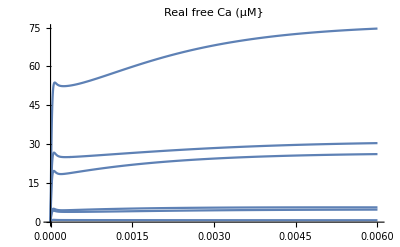

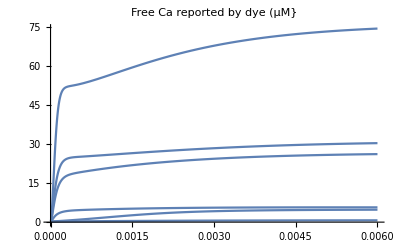

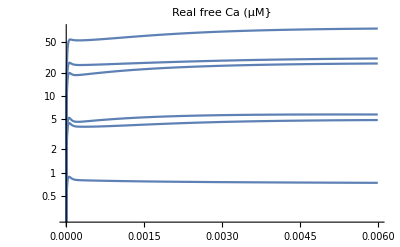

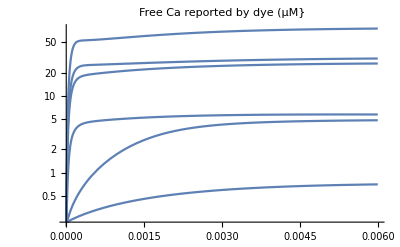

{7.03073×10^-7,4.79194×10^-6,5.70182×10^-6,0.0000262105,0.0000304385,0.0000745861}

```mathematica
Plot[10^6*CaListReal,{tt,0,TimeWindow},PlotLabel->"Real free Ca (µM}"]
Plot[10^6*CaListDye,{tt,0,TimeWindow},PlotLabel->"Free Ca reported by dye (µM}"]
LogPlot[10^6*CaListReal,{tt,0,TimeWindow},PlotLabel->"Real free Ca (µM}"]
LogPlot[10^6*CaListDye,{tt,0,TimeWindow},PlotLabel->"Free Ca reported by dye (µM}"]
CaListDyePeak=Table[NMaximize[{CaListDye[[nn]][[1]][[1]],0≤tt≤TimeWindow},tt][[1]],{nn,Length[CaListDye]}](*"[[1]][[1]]" is neede to get rid of these brackets {{}}*)
```

```mathematica
runs=Length[CaListDyePeak];
```

# Release scheme and parameters

## Define release scheme A

```mathematica
nStates=7;
matA=Table[0,{nStates},{nStates}];
```

### forward rates

```mathematica
from=1;(*0 ca bound*)
kk=5konA;
matA[[from+1,from]]+=kk;matA[[from,from]]+=-kk;

from=2;
kk=4 konA;
matA[[from+1,from]]+=kk;matA[[from,from]]+=-kk;

from=3;
kk=3 konA;
matA[[from+1,from]]+=kk;matA[[from,from]]+=-kk;

from=4;
kk=2 konA;
matA[[from+1,from]]+=kk;matA[[from,from]]+=-kk;

from=5;(*4 ca bound*)
kk=konA;
matA[[from+1,from]]+=kk;matA[[from,from]]+=-kk;

from=6;(*5 ca bound*)
kk=gammaA;
matA[[from+1,from]]+=kk;matA[[from,from]]+=-kk;
```

### backwards rates

```mathematica
from=2;(*1 ca bound*)
kk=koffA bA^0;
matA[[from-1,from]]+=kk;matA[[from,from]]+=-kk;

from=3;
kk=2 koffA bA^1;
matA[[from-1,from]]+=kk;matA[[from,from]]+=-kk;

from=4;
kk=3 koffA bA^2;
matA[[from-1,from]]+=kk;matA[[from,from]]+=-kk;

from=5;
kk=4 koffA bA^3;
matA[[from-1,from]]+=kk;matA[[from,from]]+=-kk;

from=6;(*5 ca bound*)
kk=5 koffA bA^4;
matA[[from-1,from]]+=kk;matA[[from,from]]+=-kk;
```

### outflux from matrix

```mathematica
matA[[1,1]]+=-kunprimA-kprimB;
 (*due to multiplication with ss1A[t] in mat.ss it results in:
-kunprimA ss1A[t] -kprimB ss1A[t]
 *)
```

### influx in matrix

```mathematica
matA[[1,1]]+=kprimA(1-ss1A[t])/ss1A[t]+kunprimB ss1B[t]/ss1A[t];
(* due to multiplication with ss1A[t] in mat.ss it results in:
 kprimA + kunprimB ss1B[t] *)
```

### Matrix

```mathematica
matA//TableForm
```

-5 konA-kprimB-kunprimA+(kprimA (1-ss1A[t]))/ss1A[t]+(kunprimB ss1B[t])/ss1A[t] | koffA | 0 | 0 | 0 | 0 | 0
5 konA | -koffA-4 konA | 2 bA koffA | 0 | 0 | 0 | 0
0 | 4 konA | -2 bA koffA-3 konA | 3 bA^2 koffA | 0 | 0 | 0
0 | 0 | 3 konA | -3 bA^2 koffA-2 konA | 4 bA^3 koffA | 0 | 0
0 | 0 | 0 | 2 konA | -4 bA^3 koffA-konA | 5 bA^4 koffA | 0
0 | 0 | 0 | 0 | konA | -gammaA-5 bA^4 koffA | 0
0 | 0 | 0 | 0 | 0 | gammaA | 0

## Define release scheme B

```mathematica
nStates=7;
matB=Table[0,{nStates},{nStates}];
```

### forward rates

```mathematica
from=1;(*0 ca bound*)
kk=5konB;
matB[[from+1,from]]+=kk;matB[[from,from]]+=-kk;

from=2;
kk=4 konB;
matB[[from+1,from]]+=kk;matB[[from,from]]+=-kk;

from=3;
kk=3 konB;
matB[[from+1,from]]+=kk;matB[[from,from]]+=-kk;

from=4;
kk=2 konB;
matB[[from+1,from]]+=kk;matB[[from,from]]+=-kk;

from=5;(*4 ca bound*)
kk=konB;
matB[[from+1,from]]+=kk;matB[[from,from]]+=-kk;

from=6;(*5 ca bound*)
kk=gammaB;
matB[[from+1,from]]+=kk;matB[[from,from]]+=-kk;
```

### backwards rates

```mathematica
from=2;(*1 ca bound*)
kk=koffB bB^0;
matB[[from-1,from]]+=kk;matB[[from,from]]+=-kk;

from=3;
kk=2 koffB bB^1;
matB[[from-1,from]]+=kk;matB[[from,from]]+=-kk;

from=4;
kk=3 koffB bB^2;
matB[[from-1,from]]+=kk;matB[[from,from]]+=-kk;

from=5;
kk=4 koffB bB^3;
matB[[from-1,from]]+=kk;matB[[from,from]]+=-kk;

from=6;(*5 ca bound*)
kk=5 koffB bB^4;
matB[[from-1,from]]+=kk;matB[[from,from]]+=-kk;
```

### outflux from matrix

```mathematica
matB[[1,1]]+=-kunprimB;
(* due to multiplication with ss1B[t] in mat.ss it results in:
-kunprimB ss1B[t]
*)
```

### influx in matrix

```mathematica
matB[[1,1]]+=kprimB ss1A[t]/ss1B[t];
(* due to multiplication with ss1B[t] in mat.ss it results in:
kprimB ss1A[t]
*)
```

### Matrix

```mathematica
matB//TableForm
```

-5 konB-kunprimB+(kprimB ss1A[t])/ss1B[t] | koffB | 0 | 0 | 0 | 0 | 0
5 konB | -koffB-4 konB | 2 bB koffB | 0 | 0 | 0 | 0
0 | 4 konB | -2 bB koffB-3 konB | 3 bB^2 koffB | 0 | 0 | 0
0 | 0 | 3 konB | -3 bB^2 koffB-2 konB | 4 bB^3 koffB | 0 | 0
0 | 0 | 0 | 2 konB | -4 bB^3 koffB-konB | 5 bB^4 koffB | 0
0 | 0 | 0 | 0 | konB | -gammaB-5 bB^4 koffB | 0
0 | 0 | 0 | 0 | 0 | gammaB | 0

## Parameters of release scheme

```mathematica
q10=2.3;
tempFact=q10^((37-24)/10);
```

```mathematica
Clear[caFunc,konSchemeA,konSchemeB];(*Clear is needed if the cell is exectued for a 2nd time when caFunc is already set to a value or an Interpolationfunction*)

caRest=CaRest;(*227nM see above*)

(*slow ves*)
affinityFactorA=3.0;
konSchemeA=0.5*caFunc[t] Sqrt[affinityFactorA] tempFact 1.*^8;(*M^-1 s^-1*)
koffSchemeA=10.*(1/Sqrt[affinityFactorA])tempFact 15000.;(*s^-1*)
gammaSchemeA=tempFact 6000.;(*s^-1*)
bSchemeA=0.25;

KdA=2.*^-6;
kprimSchemeA =30. +  0.*30.*(caFunc[t]/(KdA+caFunc[t])) ;
kunprimSchemeA=30. +  0.*30.*(caRest/(KdA+caRest)) ;

(*fast ves*)
affinityFactorB=3.0;
konSchemeB=caFunc[t] Sqrt[affinityFactorB] tempFact 1.*^8;(*M^-1 s^-1*)
koffSchemeB=(1/Sqrt[affinityFactorB])tempFact 15000.;(*s^-1*)
gammaSchemeB=tempFact 6000.;(*s^-1*)
bSchemeB=0.25;

KdB=2.*^-6;
kprimSchemeB =0.5+  30.*(caFunc[t]/(KdB+caFunc[t])) ;
kunprimSchemeB=0.5+  30.*(caRest/(KdB+caRest)) ;


repl={
konA -> konSchemeA,
koffA -> koffSchemeA ,
gammaA -> gammaSchemeA ,
 bA-> bSchemeA,

kprimA-> kprimSchemeA ,
kunprimA-> kunprimSchemeA ,


konB-> konSchemeB,
koffB -> koffSchemeB ,
gammaB -> gammaSchemeB ,
 bB-> bSchemeB,

kprimB-> kprimSchemeB ,
kunprimB-> kunprimSchemeB 
};
```

```mathematica
tauOfDecayOfUncagedCa=0.4;
```

## Initial occupancy

```mathematica
(*test initial equilibrium occupancy*)
caFunc[t_]:=caTmp;
ss0AInitial=kprimSchemeA/kunprimSchemeA;
ss0BInitial=(kprimSchemeA/kunprimSchemeA)*(kprimSchemeB/kunprimSchemeB);
(ss0AInitial/.caTmp->180*^-9)
(ss0AInitial/.caTmp->30*^-9)
(ss0AInitial/.caTmp->180*^-9)/(ss0AInitial/.caTmp->30*^-9)
(ss0BInitial/.caTmp->180*^-9)
(ss0BInitial/.caTmp->30*^-9)
(ss0BInitial/.caTmp->180*^-9)/(ss0BInitial/.caTmp->30*^-9)
```

1.

1.

1.

0.836742

0.26514

3.15584

```mathematica
(*calualte initial equilibrium occupancy*)
caFunc[t_]:=caRest;
ss0AInitial=kprimSchemeA/kunprimSchemeA;
ss0BInitial=(kprimSchemeA/kunprimSchemeA)*(kprimSchemeB/kunprimSchemeB);
```

## Diff eq.

```mathematica
Clear[caFunc,eq];(*Clear is needed if the cell is exectued for a 2nd time when caFunc is already set to a value or an Interpolationfunction*)
ssA[t_]={ss1A[t],ss2A[t],ss3A[t],ss4A[t],ss5A[t],ss6A[t],ss7A[t]};
ssB[t_]={ss1B[t],ss2B[t],ss3B[t],ss4B[t],ss5B[t],ss6B[t],ss7B[t]};
eq={
ssA'[t]==(matA/.repl).ssA[t],
ssA[0]=={ss0AInitial,0,0,0,0,0,0},

ssB'[t]==(matB/.repl).ssB[t],
ssB[0]=={ss0BInitial,0,0,0,0,0,0}
};
```

## Solve all states

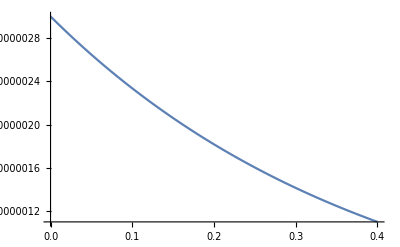

```mathematica
caFunc[t_]:=3*^-6*Exp[-t/tauOfDecayOfUncagedCa];
Plot[caFunc[t],{t,0,0.4},PlotRange->All]
```

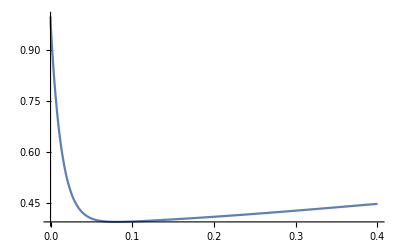

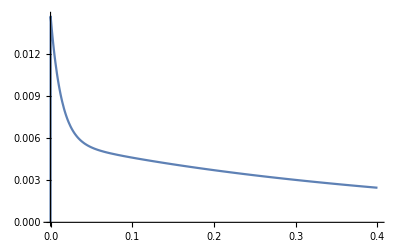

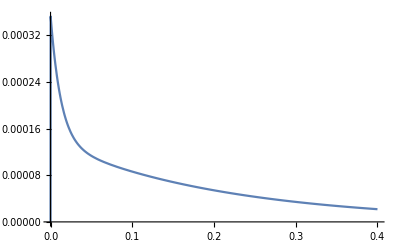

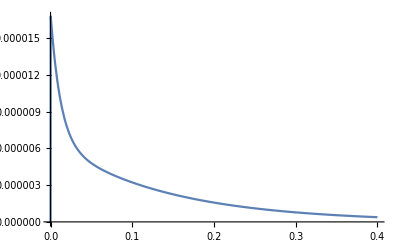

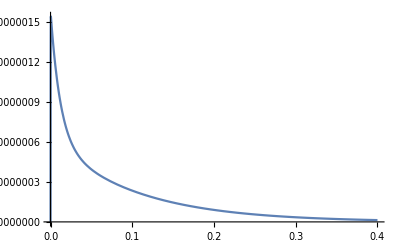

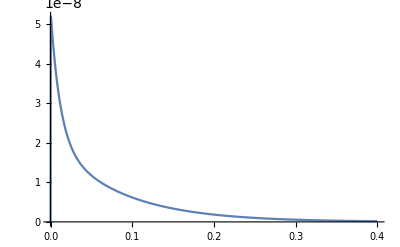

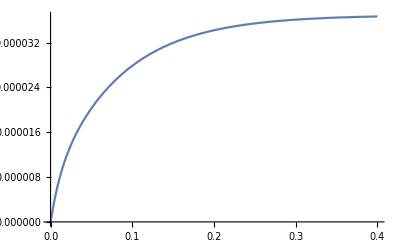

-----------------------------------------------------------------------

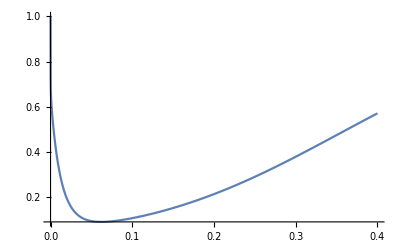

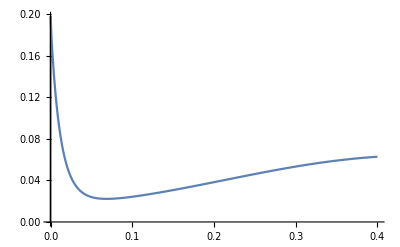

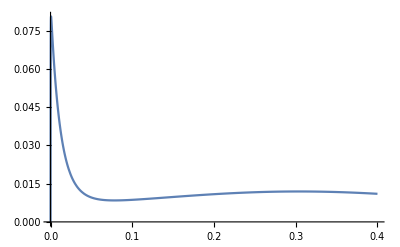

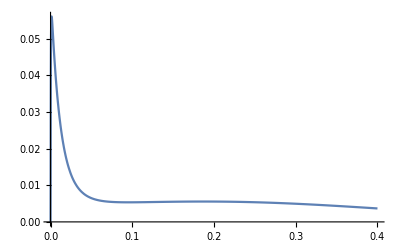

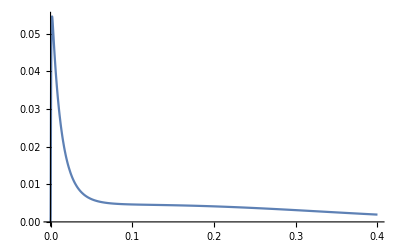

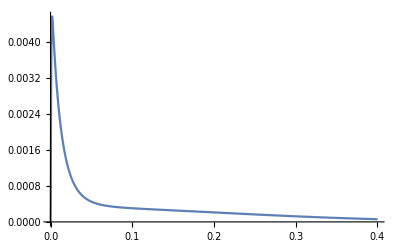

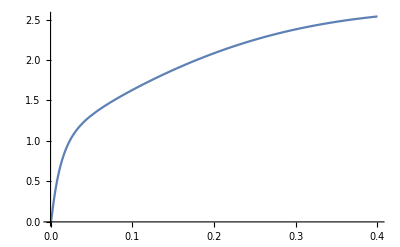

```mathematica
myNDSolveResults=NDSolve[eq,{ss1A,ss2A,ss3A,ss4A,ss5A,ss6A,ss7A,ss1B,ss2B,ss3B,ss4B,ss5B,ss6B,ss7B},{t,0,10.}];tEndForPlot=.4;
Plot[(ss1A[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss2A[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss3A[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss4A[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss5A[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss6A[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss7A[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Print["-----------------------------------------------------------------------"]
Plot[(ss1B[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss2B[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss3B[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss4B[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss5B[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss6B[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss7B[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
```

# Loop

## make lists for later

```mathematica
simCaList=Table[0,{runs}];
simParamNv=Table[0,{7},{runs}];
```

### C5

```mathematica
baselineC5=Table[{ttt,0},{ttt,cursorStart,-1*^-6,dtOfDataC5}];
(*List to save data within loop*)
(*ca; tau; number of released vesilces at time=cursorEnd; delay*)
simParamNoiseC5=Table[0,{numberOfFitParamToBeSaved},{noiseRepeats}];
simParamMedianC5=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile1C5=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile2C5=Table[0,{numberOfFitParamToBeSaved},{runs}];
```

### C10

```mathematica
baselineC10=Table[{ttt,0},{ttt,cursorStart,-1*^-6,dtOfDataC10}];
(*List to save data within loop*)
(*ca; tau; number of released vesilces at time=cursorEnd; delay*)
simParamNoiseC10=Table[0,{numberOfFitParamToBeSaved},{noiseRepeats}];
simParamMedianC10=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile1C10=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile2C10=Table[0,{numberOfFitParamToBeSaved},{runs}];
```

### D

```mathematica
baselineD=Table[{ttt,0},{ttt,cursorStart,-1*^-6,dtOfDataD}];
(*List to save data within loop*)
(*ca; tau; number of released vesilces at time=cursorEnd; delay*)
simParamNoiseD=Table[0,{numberOfFitParamToBeSaved},{noiseRepeats}];
simParamMedianD=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile1D=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile2D=Table[0,{numberOfFitParamToBeSaved},{runs}];
```

### Long

```mathematica
baselineLong=Table[{ttt,0},{ttt,-0.05,-1*^-6,dtOfDataLong}];
```

## Loop

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 0.703073 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

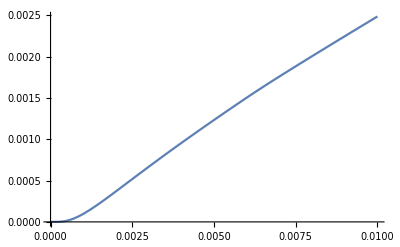

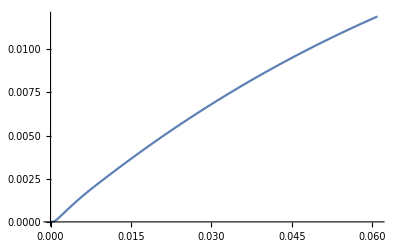

-------------------------------------------------------------------------- C5

-------------------------------------------------------------------------- C10

-------------------------------------------------------------------------- D

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 4.79194 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

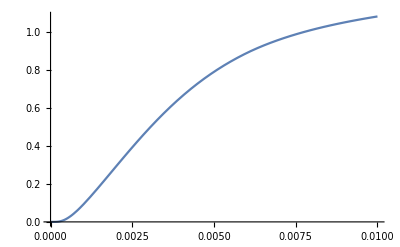

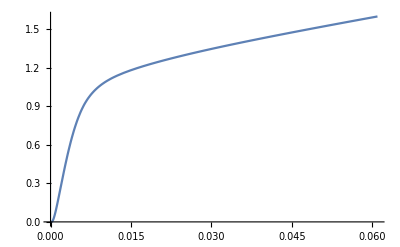

-------------------------------------------------------------------------- C5

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

take mono

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

take mono

take mono

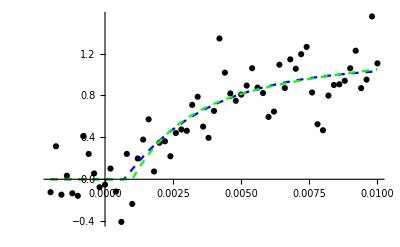

Mono: chi2 = 2.96309     d = 2.96309     a = 1.08303     t = 0.00307561

Bi: ratio chi2Mono/chi2Bi = 1.00705     d = 0.001     a = 2.66801     a1 = 0.753421     t1 =0.00177641     t2 = 0.0525808

Quantile::empt: Argument {} should be a non-empty list.

General::stop: Further output of Quantile::empt will be suppressed during this calculation.

-------------------------------------------------------------------------- C10

take mono

take mono

take mono

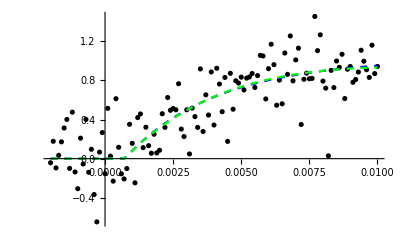

Mono: chi2 = 7.13307     d = 7.13307     a = 1.01403     t = 0.00337532

Bi: ratio chi2Mono/chi2Bi = 1.00335     d = 0.0007     a = 0.537452     a1 = 2.0822     t1 =0.00508527     t2 = 0.0123731

-------------------------------------------------------------------------- D

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

take mono

take mono

take mono

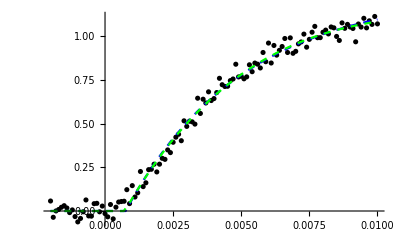

Mono: chi2 = 0.175917     d = 0.175917     a = 1.23782     t = 0.00428099

Bi: ratio chi2Mono/chi2Bi = 1.04785     d = 0.000729688     a = 0.531413     a1 = 3.07318     t1 =0.00683306     t2 = 0.0145241

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 5.70182 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

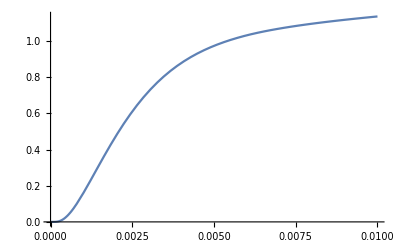

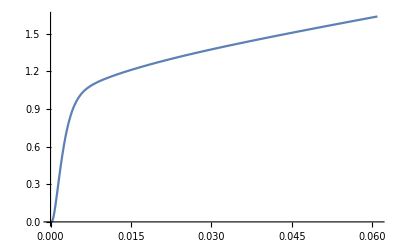

-------------------------------------------------------------------------- C5

take mono

take mono

take mono

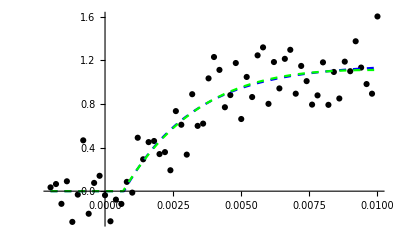

Mono: chi2 = 2.47782     d = 2.47782     a = 1.16243     t = 0.00257036

Bi: ratio chi2Mono/chi2Bi = 1.0028     d = 0.000663083     a = 0.962649     a1 = 5.53286     t1 =0.00430774     t2 = 0.00528536

-------------------------------------------------------------------------- C10

take mono

take mono

take mono

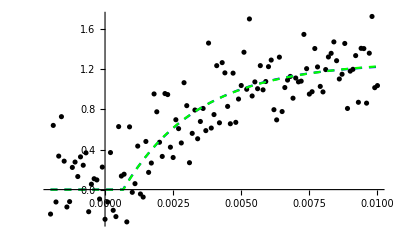

Mono: chi2 = 8.54551     d = 8.54551     a = 1.26908     t = 0.00278213

Bi: ratio chi2Mono/chi2Bi = 1.00005     d = 0.000672742     a = 1.3105     a1 = 1.08952     t1 =0.00250859     t2 = 0.00668579

-------------------------------------------------------------------------- D

take mono

take mono

take mono

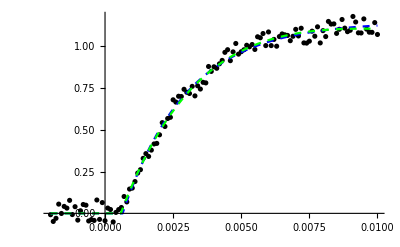

Mono: chi2 = 0.161382     d = 0.161382     a = 1.14624     t = 0.00236594

Bi: ratio chi2Mono/chi2Bi = 1.04593     d = 0.000581982     a = 0.957308     a1 = 3.21524     t1 =0.00382601     t2 = 0.00561116

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 26.2105 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

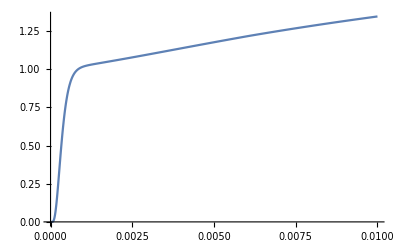

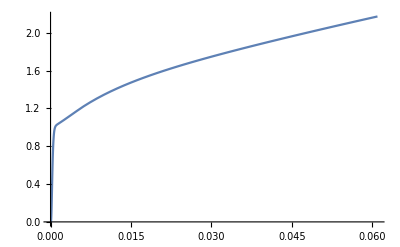

-------------------------------------------------------------------------- C5

General::munfl: Exp[-788.402] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1576.25] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2364.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

take bi

take bi

take mono

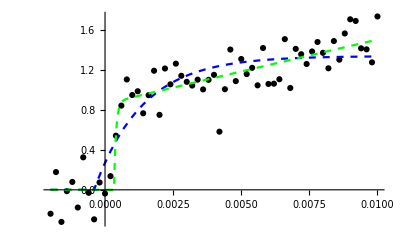

Mono: chi2 = 2.70432     d = 2.70432     a = 1.33533     t = 0.00176702

Bi: ratio chi2Mono/chi2Bi = 1.51932     d = 0.00032778     a = 21.0452     a1 = 0.8795     t1 =0.0000772609     t2 = 0.30957

-------------------------------------------------------------------------- C10

take bi

take bi

take bi

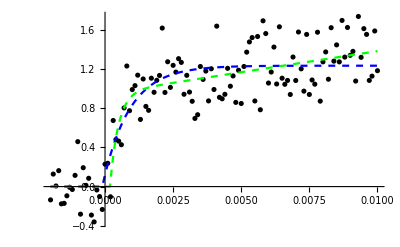

Mono: chi2 = 6.98349     d = 6.98349     a = 1.23306     t = 0.00097935

Bi: ratio chi2Mono/chi2Bi = 1.10818     d = 0.000183393     a = 19.0487     a1 = 0.957703     t1 =0.000305464     t2 = 0.41421

-------------------------------------------------------------------------- D

take bi

take bi

take bi

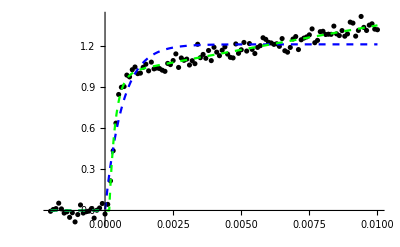

Mono: chi2 = 0.801939     d = 0.801939     a = 1.2127     t = 0.000633724

Bi: ratio chi2Mono/chi2Bi = 5.47494     d = 0.000153394     a = 4.99995     a1 = 0.991888     t1 =0.000223056     t2 = 0.104748

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 30.4385 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

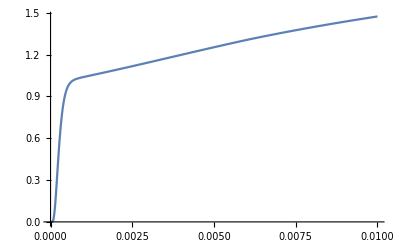

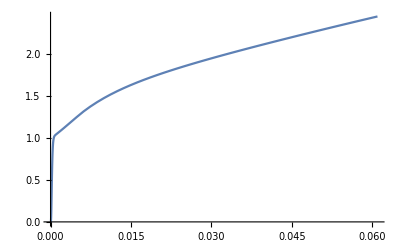

-------------------------------------------------------------------------- C5

take mono

take bi

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

take bi

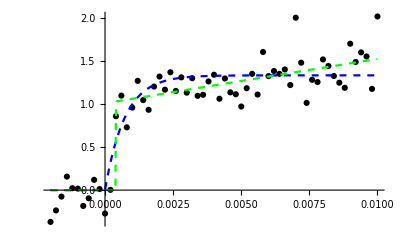

Mono: chi2 = 2.85294     d = 2.85294     a = 1.33147     t = 0.000726217

Bi: ratio chi2Mono/chi2Bi = 1.30575     d = 0.000384815     a = 19.3501     a1 = 1.02791     t1 =8.47328×10^-6     t2 = 0.352122

-------------------------------------------------------------------------- C10

take mono

take mono

take mono

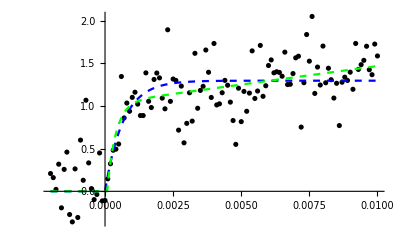

Mono: chi2 = 10.5612     d = 10.5612     a = 1.29638     t = 0.000664938

Bi: ratio chi2Mono/chi2Bi = 1.09687     d = 0.000077443     a = 21.7689     a1 = 1.03527     t1 =0.000315449     t2 = 0.470737

-------------------------------------------------------------------------- D

take bi

take bi

take bi

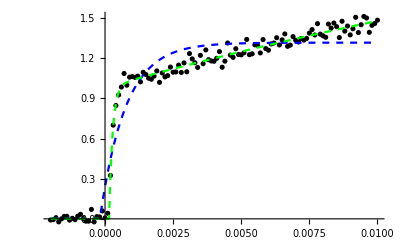

Mono: chi2 = 1.39955     d = 1.39955     a = 1.31664     t = 0.000939448

Bi: ratio chi2Mono/chi2Bi = 8.83763     d = 0.000149554     a = 2.78601     a1 = 0.988914     t1 =0.000128252     t2 = 0.0309468

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 74.5861 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

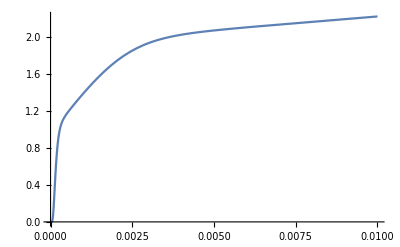

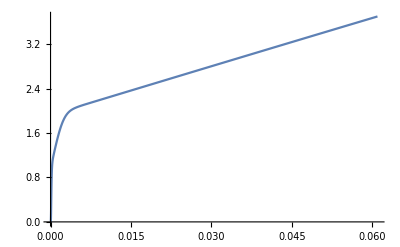

-------------------------------------------------------------------------- C5

take mono

take bi

take bi

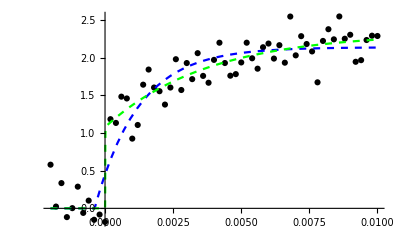

Mono: chi2 = 3.78636     d = 3.78636     a = 2.13923     t = 0.00160829

Bi: ratio chi2Mono/chi2Bi = 1.49132     d = 4.60679×10^-6     a = 2.32967     a1 = 1.08023     t1 =3.89614×10^-6     t2 = 0.00376319

-------------------------------------------------------------------------- C10

take mono

take bi

take mono

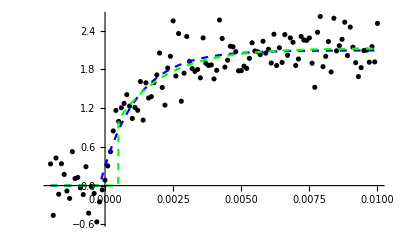

Mono: chi2 = 8.25029     d = 8.25029     a = 2.09501     t = 0.00131592

Bi: ratio chi2Mono/chi2Bi = 0.803446     d = 0.00048757     a = 2.12862     a1 = 1.01187     t1 =3.35749×10^-6     t2 = 0.00176021

-------------------------------------------------------------------------- D

take bi

take bi

take bi

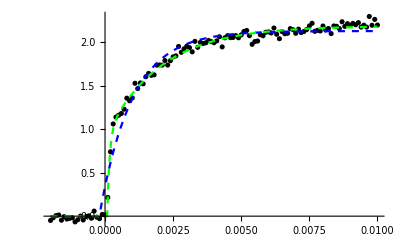

Mono: chi2 = 0.883126     d = 0.883126     a = 2.12918     t = 0.00120572

Bi: ratio chi2Mono/chi2Bi = 4.48386     d = 0.0000795971     a = 2.18666     a1 = 0.952218     t1 =0.0000883538     t2 = 0.0019903

```mathematica
For[r=1,r≤runs,r+=1,
myCaNow=CaListDyePeak[[r]];
lastSimulatedCaListReal=CaListReal[[r]][[1]][[1]]/.tt->TimeWindow;(*"[[1]][[1]]" is neede to get rid of these brackets {{}}*)
Print["-------------------------------------------------------------------------------------------------------------"];Print["----------------    Ca = ",1*^6 myCaNow," uM         --------------------------------------------------------"];Print["-------------------------------------------------------------------------------------------------------------"];
simCaList[[r]]=myCaNow;
caFunc[ttt_]:=If[ttt<TimeWindow,
CaListReal[[r]][[1]][[1]]/.tt->ttt,(*tt because this is the symbol used in "Calculate Ca transients"*)
lastSimulatedCaListReal*Exp[-ttt/tauOfDecayOfUncagedCa]
];
(* solve Diff Eq.: *)
myNDSolveResults=NDSolve[eq,{ss7A,ss7B},{t,0,0.4}]; 
(* plot results: *)
fused[t_]:=(ss7A[t]+ss7B[t]);
Plot[(fused[t]/.myNDSolveResults),{t,0,cursorEnd},PlotRange->All]//Print;
Plot[(fused[t]/.myNDSolveResults),{t,0,cursorEndLong},PlotRange->All]//Print;
If[exportYes==1,
toExport=Table[{t,(fused[t]/.myNDSolveResults)[[1]]},{t,0.,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" withoutNoise.txt",toExport,"Table"];
];
(* sample data and add baseline: --------*)
tmpCumRelC5=Table[{ttt,(fused[ttt]/.myNDSolveResults)[[1]]},{ttt,0.,cursorEnd,dtOfDataC5}];
tmpToFitC5=Catenate[{baselineC5,tmpCumRelC5}];
tmpCumRelC10=Table[{ttt,(fused[ttt]/.myNDSolveResults)[[1]]},{ttt,0.,cursorEnd,dtOfDataC10}];
tmpToFitC10=Catenate[{baselineC10,tmpCumRelC10}];
tmpCumRelD=Table[{ttt,(fused[ttt]/.myNDSolveResults)[[1]]},{ttt,0.,cursorEnd,dtOfDataD}];
tmpToFitD=Catenate[{baselineD,tmpCumRelD}];
tmpCumRelLong=Table[{ttt,(fused[ttt]/.myNDSolveResults)[[1]]},{ttt,0.,cursorEndLong,dtOfDataLong}];
tmpToFitLong=Catenate[{baselineLong,tmpCumRelLong}];

(*---------    get amplitude without noise and without fitting -----------------*)
For[NvCount=1,NvCount≤7,NvCount+=1,
simParamNv[[NvCount,r]]=(fused[timeOfNv[[NvCount]]]/.myNDSolveResults)[[1]];(* the [[1]] is somehow needed to get rid of a list structure probably related to the interpolate function*)
];

(*--------------   Startvalues for fit the same for all C5 C10 and D -------------*)
caAdjustedTau1Guess=tau1Guess/((myCaNow/10.*^-6)^4);
caAdjustedTau1Guess=tau1Guess/((myCaNow/10.*^-6)^1);
caAdjustedTau2Guess=10 caAdjustedTau1Guess;
caAdjustedDelayGuess=delayGuess/((myCaNow/10.*^-6)^1);

(*---------    Fitting of data, saving of results, and plotting-----------------*)
(*-----------------------------------------------------------------------------*)
(*--------------------------------------    C5     ----------------------------*)
(*-----------------------------------------------------------------------------*)
Print["-------------------------------------------------------------------------- C5"];
(*check that signal is large enough relative to noise to obtain useful fit results. If not, do not do fitting and set everything to {}*)
If[simParamNv[[5,r]] > signalToNoiseRatioC5 myNoiseC5,(*add noise several times and do the fitting and than average the results*)
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
(*Print[noiseN];*)
tmpToFitNoise=Transpose[{tmpToFitC5[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseC5]]&/@tmpToFitC5[[All,2]]}];
(*fit mono-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoise, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultMono=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC5[[1,noiseN]]=0;(*not used anymore*)
simParamNoiseC5[[2,noiseN]]=fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
(*Print[fitResultsTMP["ANOVATableSumsOfSquares"]];*)
simParamNoiseC5[[3,noiseN]]=(delayMono/.fitResultMono)[[1]];
simParamNoiseC5[[4,noiseN]]=((ampMono/.fitResultMono))[[1]];
simParamNoiseC5[[5,noiseN]]=(1/(tau1Mono/.fitResultMono))[[1]];
(*fit bi-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoise, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultBi=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC5[[6,noiseN]]=simParamNoiseC5[[2,noiseN]]/fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
simParamNoiseC5[[7,noiseN]]=(delay/.fitResultBi)[[1]];
simParamNoiseC5[[8,noiseN]]=((amp/.fitResultBi))[[1]];
simParamNoiseC5[[9,noiseN]]=((amp amp1/.fitResultBi))[[1]];(*relative amp1*)
simParamNoiseC5[[10,noiseN]]=(1/(tau1/.fitResultBi))[[1]];
simParamNoiseC5[[11,noiseN]]=(1/(tau2/.fitResultBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should imporve(=decrease) by >10%*)
(simParamNoiseC5[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseC5[[11,noiseN]]/simParamNoiseC5[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseC5[[12,noiseN]]=simParamNoiseC5[[7,noiseN]];(*delay*)
simParamNoiseC5[[13,noiseN]]=simParamNoiseC5[[8,noiseN]];(*amp*)
simParamNoiseC5[[14,noiseN]]=simParamNoiseC5[[9,noiseN]];(*amp1*)
simParamNoiseC5[[15,noiseN]]=simParamNoiseC5[[10,noiseN]];(*tau1*)
simParamNoiseC5[[16,noiseN]]=simParamNoiseC5[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseC5[[12,noiseN]]=simParamNoiseC5[[3,noiseN]];(*delay*)
simParamNoiseC5[[13,noiseN]]=simParamNoiseC5[[4,noiseN]];(*amp*)
simParamNoiseC5[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseC5[[15,noiseN]]=simParamNoiseC5[[5,noiseN]];(*tau1*)
simParamNoiseC5[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoise,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultMono,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultBi,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 data.txt",tmpToFitNoise,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultMono)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 fitMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultBi)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 fitBi.txt",toExport,"Table"];
];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseC5[[2,noiseN]],"     d = ",simParamNoiseC5[[2,noiseN]],"     a = ",simParamNoiseC5[[4,noiseN]],"     t = ",1/simParamNoiseC5[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseC5[[6,noiseN]],"     d = ",simParamNoiseC5[[7,noiseN]],"     a = ",simParamNoiseC5[[8,noiseN]],"     a1 = ",simParamNoiseC5[[9,noiseN]],"     t1 =",1/simParamNoiseC5[[10,noiseN]],"     t2 = ",1/simParamNoiseC5[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC5[[p,r]]=Median[simParamNoiseC5[[p,All]]/.NaN->Sequence[]];
simParamQuantile1C5[[p,r]]=Quantile[simParamNoiseC5[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2C5[[p,r]]=Quantile[simParamNoiseC5[[p,All]]/.NaN->Sequence[],myQuantile2];
];

(*if tau1 merge > 10 ms, use long trace for fitting*)
If[(1/simParamMedianC5[[15,r]])>0.01,
Print["Long trace was used for fitting."];
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
tmpToFitNoiseLong=Transpose[{tmpToFitLong[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseLong]]&/@tmpToFitLong[[All,2]]}];
(*fit mono-exp to Long trace*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoiseLong, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongMono=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC5[[2,noiseN]]=fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
(*Print[fitResultsTMP["ANOVATableSumsOfSquares"]];*)
simParamNoiseC5[[3,noiseN]]=(delayMono/.fitResultLongMono)[[1]];
simParamNoiseC5[[4,noiseN]]=((ampMono/.fitResultLongMono))[[1]];
simParamNoiseC5[[5,noiseN]]=(1/(tau1Mono/.fitResultLongMono))[[1]];
(*fit bi-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoiseLong, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongBi=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC5[[6,noiseN]]=simParamNoiseC5[[2,noiseN]]/fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
simParamNoiseC5[[7,noiseN]]=(delay/.fitResultLongBi)[[1]];
simParamNoiseC5[[8,noiseN]]=((amp/.fitResultLongBi))[[1]];
simParamNoiseC5[[9,noiseN]]=((amp amp1/.fitResultLongBi))[[1]];(*relative amp1*)
simParamNoiseC5[[10,noiseN]]=(1/(tau1/.fitResultLongBi))[[1]];
simParamNoiseC5[[11,noiseN]]=(1/(tau2/.fitResultLongBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should imporve(=decrease) by >10%*)
(simParamNoiseC5[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseC5[[11,noiseN]]/simParamNoiseC5[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultLongBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultLongBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseC5[[12,noiseN]]=simParamNoiseC5[[7,noiseN]];(*delay*)
simParamNoiseC5[[13,noiseN]]=simParamNoiseC5[[8,noiseN]];(*amp*)
simParamNoiseC5[[14,noiseN]]=simParamNoiseC5[[9,noiseN]];(*amp1*)
simParamNoiseC5[[15,noiseN]]=simParamNoiseC5[[10,noiseN]];(*tau1*)
simParamNoiseC5[[16,noiseN]]=simParamNoiseC5[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseC5[[12,noiseN]]=simParamNoiseC5[[3,noiseN]];(*delay*)
simParamNoiseC5[[13,noiseN]]=simParamNoiseC5[[4,noiseN]];(*amp*)
simParamNoiseC5[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseC5[[15,noiseN]]=simParamNoiseC5[[5,noiseN]];(*tau1*)
simParamNoiseC5[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoiseLong,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultLongMono,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultLongBi,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 dataLong.txt",tmpToFitNoiseLong,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultLongMono)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 fitLongMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultLongBi)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 fitLongBi.txt",toExport,"Table"];

];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseC5[[2,noiseN]],"     d = ",simParamNoiseC5[[3,noiseN]],"     a = ",simParamNoiseC5[[4,noiseN]],"     t = ",1/simParamNoiseC5[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseC5[[6,noiseN]],"     d = ",simParamNoiseC5[[7,noiseN]],"     a = ",simParamNoiseC5[[8,noiseN]],"     a1 = ",simParamNoiseC5[[9,noiseN]],"     t1 =",1/simParamNoiseC5[[10,noiseN]],"     t2 = ",1/simParamNoiseC5[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC5[[p,r]]=Median[simParamNoiseC5[[p,All]]/.NaN->Sequence[]];
simParamQuantile1C5[[p,r]]=Quantile[simParamNoiseC5[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2C5[[p,r]]=Quantile[simParamNoiseC5[[p,All]]/.NaN->Sequence[],myQuantile2];
];
];

,(*else: signal is not large enough*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC5[[p,r]]={};
simParamQuantile1C5[[p,r]]={};
simParamQuantile2C5[[p,r]]={};
];
];


(*---------    Fitting of data, saving of results, and plotting-----------------*)
(*-----------------------------------------------------------------------------*)
(*--------------------------------------    C10     ----------------------------*)
(*-----------------------------------------------------------------------------*)
Print["-------------------------------------------------------------------------- C10"];
(*check that signal is large enough relative to noise to obtain useful fit results. If not, do not do fitting and set everything to {}*)
If[simParamNv[[5,r]] > signalToNoiseRatioC10 myNoiseC10,(*add noise and do the fitting several times and then average the results*)
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
(*Print[noiseN];*)
tmpToFitNoise=Transpose[{tmpToFitC10[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseC10]]&/@tmpToFitC10[[All,2]]}];
(*fit mono-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoise, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultMono=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC10[[1,noiseN]]=0;(*not used anymore*)
simParamNoiseC10[[2,noiseN]]=fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
(*Print[fitResultsTMP["ANOVATableSumsOfSquares"]];*)
simParamNoiseC10[[3,noiseN]]=(delayMono/.fitResultMono)[[1]];
simParamNoiseC10[[4,noiseN]]=((ampMono/.fitResultMono))[[1]];
simParamNoiseC10[[5,noiseN]]=(1/(tau1Mono/.fitResultMono))[[1]];
(*fit bi-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoise, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultBi=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC10[[6,noiseN]]=simParamNoiseC10[[2,noiseN]]/fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
simParamNoiseC10[[7,noiseN]]=(delay/.fitResultBi)[[1]];
simParamNoiseC10[[8,noiseN]]=((amp/.fitResultBi))[[1]];
simParamNoiseC10[[9,noiseN]]=((amp amp1/.fitResultBi))[[1]];(*relative amp1*)
simParamNoiseC10[[10,noiseN]]=(1/(tau1/.fitResultBi))[[1]];
simParamNoiseC10[[11,noiseN]]=(1/(tau2/.fitResultBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseC10[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseC10[[11,noiseN]]/simParamNoiseC10[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseC10[[12,noiseN]]=simParamNoiseC10[[7,noiseN]];(*delay*)
simParamNoiseC10[[13,noiseN]]=simParamNoiseC10[[8,noiseN]];(*amp*)
simParamNoiseC10[[14,noiseN]]=simParamNoiseC10[[9,noiseN]];(*amp1*)
simParamNoiseC10[[15,noiseN]]=simParamNoiseC10[[10,noiseN]];(*tau1*)
simParamNoiseC10[[16,noiseN]]=simParamNoiseC10[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseC10[[12,noiseN]]=simParamNoiseC10[[3,noiseN]];(*delay*)
simParamNoiseC10[[13,noiseN]]=simParamNoiseC10[[4,noiseN]];(*amp*)
simParamNoiseC10[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseC10[[15,noiseN]]=simParamNoiseC10[[5,noiseN]];(*tau1*)
simParamNoiseC10[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoise,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultMono,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultBi,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 data.txt",tmpToFitNoise,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultMono)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 fitMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultBi)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 fitBi.txt",toExport,"Table"];
];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseC10[[2,noiseN]],"     d = ",simParamNoiseC10[[2,noiseN]],"     a = ",simParamNoiseC10[[4,noiseN]],"     t = ",1/simParamNoiseC10[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseC10[[6,noiseN]],"     d = ",simParamNoiseC10[[7,noiseN]],"     a = ",simParamNoiseC10[[8,noiseN]],"     a1 = ",simParamNoiseC10[[9,noiseN]],"     t1 =",1/simParamNoiseC10[[10,noiseN]],"     t2 = ",1/simParamNoiseC10[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC10[[p,r]]=Median[simParamNoiseC10[[p,All]]/.NaN->Sequence[]];
simParamQuantile1C10[[p,r]]=Quantile[simParamNoiseC10[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2C10[[p,r]]=Quantile[simParamNoiseC10[[p,All]]/.NaN->Sequence[],myQuantile2];
];

(*if tau1 merge > 10 ms, use long trace for fitting*)
If[(1/simParamMedianC10[[15,r]])>0.01,
Print["Long trace was used for fitting."];
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
tmpToFitNoiseLong=Transpose[{tmpToFitLong[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseLong]]&/@tmpToFitLong[[All,2]]}];
(*fit mono-exp to Long trace*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoiseLong, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongMono=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC10[[2,noiseN]]=fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
(*Print[fitResultsTMP["ANOVATableSumsOfSquares"]];*)
simParamNoiseC10[[3,noiseN]]=(delayMono/.fitResultLongMono)[[1]];
simParamNoiseC10[[4,noiseN]]=((ampMono/.fitResultLongMono))[[1]];
simParamNoiseC10[[5,noiseN]]=(1/(tau1Mono/.fitResultLongMono))[[1]];
(*fit bi-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoiseLong, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongBi=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC10[[6,noiseN]]=simParamNoiseC10[[2,noiseN]]/fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
simParamNoiseC10[[7,noiseN]]=(delay/.fitResultLongBi)[[1]];
simParamNoiseC10[[8,noiseN]]=((amp/.fitResultLongBi))[[1]];
simParamNoiseC10[[9,noiseN]]=((amp amp1/.fitResultLongBi))[[1]];(*relative amp1*)
simParamNoiseC10[[10,noiseN]]=(1/(tau1/.fitResultLongBi))[[1]];
simParamNoiseC10[[11,noiseN]]=(1/(tau2/.fitResultLongBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseC10[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseC10[[11,noiseN]]/simParamNoiseC10[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultLongBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultLongBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseC10[[12,noiseN]]=simParamNoiseC10[[7,noiseN]];(*delay*)
simParamNoiseC10[[13,noiseN]]=simParamNoiseC10[[8,noiseN]];(*amp*)
simParamNoiseC10[[14,noiseN]]=simParamNoiseC10[[9,noiseN]];(*amp1*)
simParamNoiseC10[[15,noiseN]]=simParamNoiseC10[[10,noiseN]];(*tau1*)
simParamNoiseC10[[16,noiseN]]=simParamNoiseC10[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseC10[[12,noiseN]]=simParamNoiseC10[[3,noiseN]];(*delay*)
simParamNoiseC10[[13,noiseN]]=simParamNoiseC10[[4,noiseN]];(*amp*)
simParamNoiseC10[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseC10[[15,noiseN]]=simParamNoiseC10[[5,noiseN]];(*tau1*)
simParamNoiseC10[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoiseLong,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultLongMono,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultLongBi,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 dataLong.txt",tmpToFitNoiseLong,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultLongMono)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 fitLongMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultLongBi)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 fitLongBi.txt",toExport,"Table"];

];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseC10[[2,noiseN]],"     d = ",simParamNoiseC10[[3,noiseN]],"     a = ",simParamNoiseC10[[4,noiseN]],"     t = ",1/simParamNoiseC10[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseC10[[6,noiseN]],"     d = ",simParamNoiseC10[[7,noiseN]],"     a = ",simParamNoiseC10[[8,noiseN]],"     a1 = ",simParamNoiseC10[[9,noiseN]],"     t1 =",1/simParamNoiseC10[[10,noiseN]],"     t2 = ",1/simParamNoiseC10[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC10[[p,r]]=Median[simParamNoiseC10[[p,All]]/.NaN->Sequence[]];
simParamQuantile1C10[[p,r]]=Quantile[simParamNoiseC10[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2C10[[p,r]]=Quantile[simParamNoiseC10[[p,All]]/.NaN->Sequence[],myQuantile2];
];
];

,(*else: signal is not large enough*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC10[[p,r]]={};
simParamQuantile1C10[[p,r]]={};
simParamQuantile2C10[[p,r]]={};
];
];

(*---------    Fitting of data, saving of results, and plotting-----------------*)
(*-----------------------------------------------------------------------------*)
(*--------------------------------------    D     ----------------------------*)
(*-----------------------------------------------------------------------------*)
Print["-------------------------------------------------------------------------- D"];
(*check that signal is large enough relative to noise to obtain useful fit results. If not, do not do fitting and set everything to {}*)
If[simParamNv[[5,r]] > signalToNoiseRatioD myNoiseD,(*add noise several times and do the fitting and than average the results*)
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
(*Print[noiseN];*)
tmpToFitNoise=Transpose[{tmpToFitD[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseD]]&/@tmpToFitD[[All,2]]}];
(*fit mono-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoise, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultMono=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseD[[1,noiseN]]=0;(*not used anymore*)
simParamNoiseD[[2,noiseN]]=fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
(*Print[fitResultsTMP["ANOVATableSumsOfSquares"]];*)
simParamNoiseD[[3,noiseN]]=(delayMono/.fitResultMono)[[1]];
simParamNoiseD[[4,noiseN]]=((ampMono/.fitResultMono))[[1]];
simParamNoiseD[[5,noiseN]]=(1/(tau1Mono/.fitResultMono))[[1]];
(*fit bi-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoise, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultBi=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseD[[6,noiseN]]=simParamNoiseD[[2,noiseN]]/fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
simParamNoiseD[[7,noiseN]]=(delay/.fitResultBi)[[1]];
simParamNoiseD[[8,noiseN]]=((amp/.fitResultBi))[[1]];
simParamNoiseD[[9,noiseN]]=((amp amp1/.fitResultBi))[[1]];(*relative amp1*)
simParamNoiseD[[10,noiseN]]=(1/(tau1/.fitResultBi))[[1]];
simParamNoiseD[[11,noiseN]]=(1/(tau2/.fitResultBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseD[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseD[[11,noiseN]]/simParamNoiseD[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseD[[12,noiseN]]=simParamNoiseD[[7,noiseN]];(*delay*)
simParamNoiseD[[13,noiseN]]=simParamNoiseD[[8,noiseN]];(*amp*)
simParamNoiseD[[14,noiseN]]=simParamNoiseD[[9,noiseN]];(*amp1*)
simParamNoiseD[[15,noiseN]]=simParamNoiseD[[10,noiseN]];(*tau1*)
simParamNoiseD[[16,noiseN]]=simParamNoiseD[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseD[[12,noiseN]]=simParamNoiseD[[3,noiseN]];(*delay*)
simParamNoiseD[[13,noiseN]]=simParamNoiseD[[4,noiseN]];(*amp*)
simParamNoiseD[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseD[[15,noiseN]]=simParamNoiseD[[5,noiseN]];(*tau1*)
simParamNoiseD[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoise,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultMono,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultBi,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D data.txt",tmpToFitNoise,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultMono)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D fitMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultBi)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D fitBi.txt",toExport,"Table"];
];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseD[[2,noiseN]],"     d = ",simParamNoiseD[[2,noiseN]],"     a = ",simParamNoiseD[[4,noiseN]],"     t = ",1/simParamNoiseD[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseD[[6,noiseN]],"     d = ",simParamNoiseD[[7,noiseN]],"     a = ",simParamNoiseD[[8,noiseN]],"     a1 = ",simParamNoiseD[[9,noiseN]],"     t1 =",1/simParamNoiseD[[10,noiseN]],"     t2 = ",1/simParamNoiseD[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianD[[p,r]]=Median[simParamNoiseD[[p,All]]/.NaN->Sequence[]];
simParamQuantile1D[[p,r]]=Quantile[simParamNoiseD[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2D[[p,r]]=Quantile[simParamNoiseD[[p,All]]/.NaN->Sequence[],myQuantile2];
];

(*if tau1 merge > 10 ms, use long trace for fitting*)
If[(1/simParamMedianD[[15,r]])>0.01,
Print["Long trace was used for fitting."];
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
tmpToFitNoiseLong=Transpose[{tmpToFitLong[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseLong]]&/@tmpToFitLong[[All,2]]}];
(*fit mono-exp to Long trace*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoiseLong, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongMono=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseD[[2,noiseN]]=fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
(*Print[fitResultsTMP["ANOVATableSumsOfSquares"]];*)
simParamNoiseD[[3,noiseN]]=(delayMono/.fitResultLongMono)[[1]];
simParamNoiseD[[4,noiseN]]=((ampMono/.fitResultLongMono))[[1]];
simParamNoiseD[[5,noiseN]]=(1/(tau1Mono/.fitResultLongMono))[[1]];
(*fit bi-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoiseLong, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongBi=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseD[[6,noiseN]]=simParamNoiseD[[2,noiseN]]/fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
simParamNoiseD[[7,noiseN]]=(delay/.fitResultLongBi)[[1]];
simParamNoiseD[[8,noiseN]]=((amp/.fitResultLongBi))[[1]];
simParamNoiseD[[9,noiseN]]=((amp amp1/.fitResultLongBi))[[1]];(*relative amp1*)
simParamNoiseD[[10,noiseN]]=(1/(tau1/.fitResultLongBi))[[1]];
simParamNoiseD[[11,noiseN]]=(1/(tau2/.fitResultLongBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseD[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseD[[11,noiseN]]/simParamNoiseD[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultLongBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultLongBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseD[[12,noiseN]]=simParamNoiseD[[7,noiseN]];(*delay*)
simParamNoiseD[[13,noiseN]]=simParamNoiseD[[8,noiseN]];(*amp*)
simParamNoiseD[[14,noiseN]]=simParamNoiseD[[9,noiseN]];(*amp1*)
simParamNoiseD[[15,noiseN]]=simParamNoiseD[[10,noiseN]];(*tau1*)
simParamNoiseD[[16,noiseN]]=simParamNoiseD[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseD[[12,noiseN]]=simParamNoiseD[[3,noiseN]];(*delay*)
simParamNoiseD[[13,noiseN]]=simParamNoiseD[[4,noiseN]];(*amp*)
simParamNoiseD[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseD[[15,noiseN]]=simParamNoiseD[[5,noiseN]];(*tau1*)
simParamNoiseD[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoiseLong,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultLongMono,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultLongBi,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D dataLong.txt",tmpToFitNoiseLong,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultLongMono)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D fitLongMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultLongBi)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D fitLongBi.txt",toExport,"Table"];

];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseD[[2,noiseN]],"     d = ",simParamNoiseD[[3,noiseN]],"     a = ",simParamNoiseD[[4,noiseN]],"     t = ",1/simParamNoiseD[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseD[[6,noiseN]],"     d = ",simParamNoiseD[[7,noiseN]],"     a = ",simParamNoiseD[[8,noiseN]],"     a1 = ",simParamNoiseD[[9,noiseN]],"     t1 =",1/simParamNoiseD[[10,noiseN]],"     t2 = ",1/simParamNoiseD[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianD[[p,r]]=Median[simParamNoiseD[[p,All]]/.NaN->Sequence[]];
simParamQuantile1D[[p,r]]=Quantile[simParamNoiseD[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2D[[p,r]]=Quantile[simParamNoiseD[[p,All]]/.NaN->Sequence[],myQuantile2];
];
];

,(*else: signal is not large enough*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianD[[p,r]]={};
simParamQuantile1D[[p,r]]={};
simParamQuantile2D[[p,r]]={};
];
];
];
```

# Plots

```mathematica
caFact=1*^6;
```

```mathematica
colorA=Green;
colorB=Red;
colorC=Blue;
```

## release rate 1/tau1 (merge of mono 1/tau and bi 1/tau1)

```mathematica
simParam=15;
```

### C5

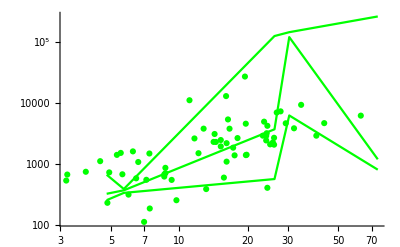

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca, dataT1C5RelRate}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau1 C5 data.txt",Transpose[{dataT1C5Ca, dataT1C5RelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]],simParamMedianC5[[simParam,All]],simParamQuantile2C5[[simParam,All]]}];
Export["plot InvTau1 C5 fit - quantiles and median.txt",toExport,"Table"];
];
```

### C10

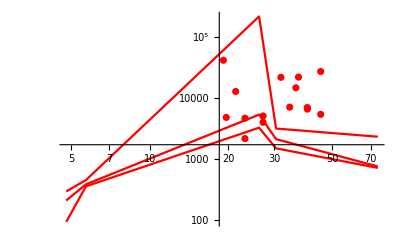

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca, dataT1C10RelRate}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau1 C10 data.txt",Transpose[{dataT1C10Ca, dataT1C10RelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]],simParamMedianC10[[simParam,All]],simParamQuantile2C10[[simParam,All]]}];
Export["plot InvTau1 C10 fit - quantiles and median.txt",toExport,"Table"];
];
```

### D

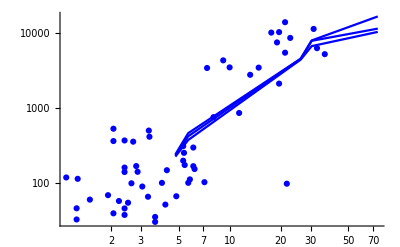

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT1DCa, dataT1DRelRate}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianD[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau1 D data.txt",Transpose[{dataT1DCa, dataT1DRelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]],simParamMedianD[[simParam,All]],simParamQuantile2D[[simParam,All]]}];
Export["plot InvTau1 D fit - quantiles and median.txt",toExport,"Table"];
];
```

### C5 and C10 and D

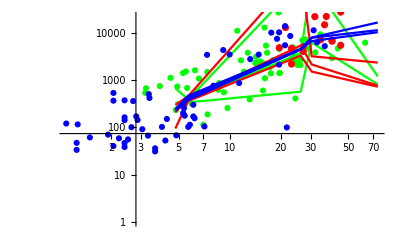

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{All,{0,10}}]
```

```mathematica
Show[gr1a,gr1b,gr1c,PlotRange->{All,{2,10}}];
```

## delay (mono and bi merged)

```mathematica
simParam=12;
```

```mathematica
Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}]//TableForm
```

0.703073 | 
4.79194 | 0.0015475
5.70182 | 0.000567899
26.2105 | 0.000149017
30.4385 | 0.000384815
74.5861 | -0.000183647

### C5

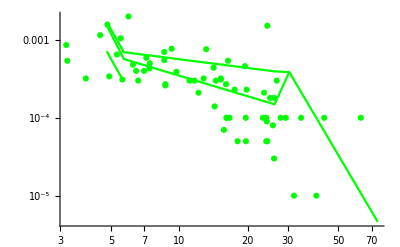

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca, dataT1C5Delay}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
If[exportYes==1,
Export["plot delay C5 data.txt",Transpose[{dataT1C5Ca, dataT1C5Delay}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]],simParamMedianC5[[simParam,All]],simParamQuantile2C5[[simParam,All]]}];
Export["plot delay C5 fit - quantiles and median.txt",toExport,"Table"];
];
```

### C10

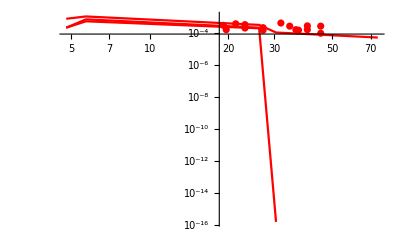

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca, dataT1C10Delay}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
If[exportYes==1,
Export["plot delay C10 data.txt",Transpose[{dataT1C10Ca, dataT1C10Delay}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]],simParamMedianC10[[simParam,All]],simParamQuantile2C10[[simParam,All]]}];
Export["plot delay C10 fit - quantiles and median.txt",toExport,"Table"];
];
```

### D

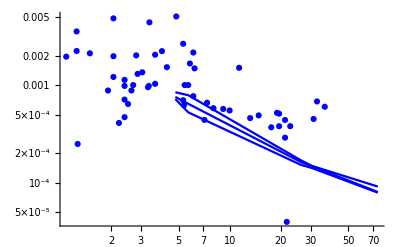

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT1DCa, dataT1DDelay}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianD[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
If[exportYes==1,
Export["plot delay D data.txt",Transpose[{dataT1DCa, dataT1DDelay}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]],simParamMedianD[[simParam,All]],simParamQuantile2D[[simParam,All]]}];
Export["plot delay D fit - quantiles and median.txt",toExport,"Table"];
];
```

### C5 and C10 and D

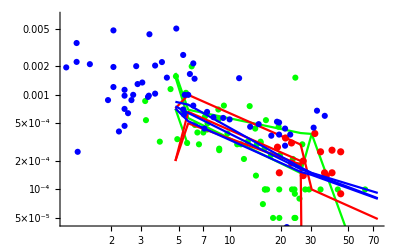

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{-10,-5}]
```

```mathematica
Show[gr1a,gr1b,gr1c,PlotRange->All];
```

## amp (merge of mono amp and bi amp)

```mathematica
simParam=13;
```

### C5

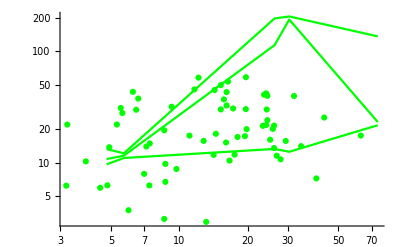

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca,dataT1C5Amplitude}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
```

### C10

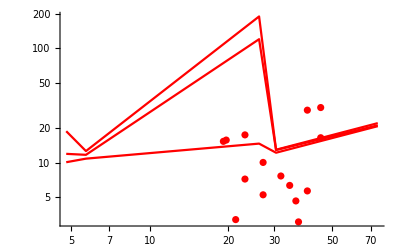

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca, dataT1C10Amplitude}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
```

### D

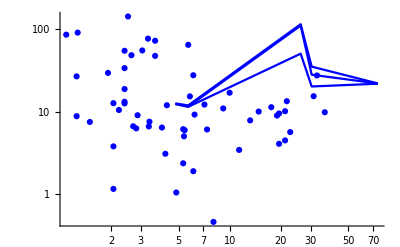

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT1DCa, dataT1DAmplitude}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianD[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
```

### C5 and C10 and D

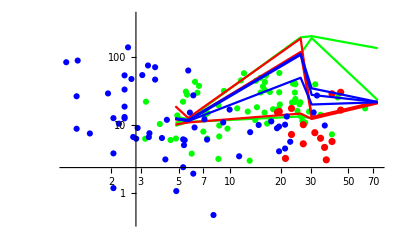

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{-1,6} ]
```

## release rate 1/tau2 of bi fits (if bi is justified)

```mathematica
simParam=16;
```

### C5

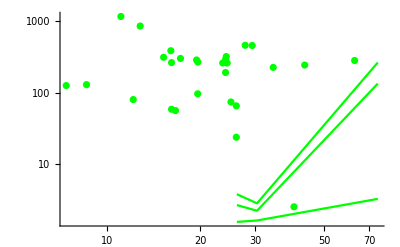

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT2C5Ca, dataT2C5RelRate}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau2 C5 data.txt",Transpose[{dataT2C5Ca, dataT2C5RelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]],simParamMedianC5[[simParam,All]],simParamQuantile2C5[[simParam,All]]}];
Export["plot InvTau2 C5 fit - quantiles and median.txt",toExport,"Table"];
];
```

### C10

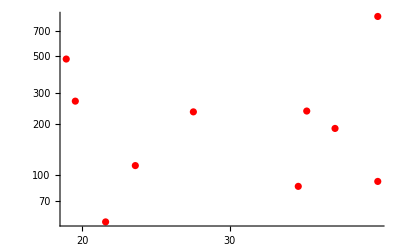

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT2C10Ca, dataT2C10RelRate}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau2 C10 data.txt",Transpose[{dataT2C10Ca, dataT2C10RelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]],simParamMedianC10[[simParam,All]],simParamQuantile2C10[[simParam,All]]}];
Export["plot InvTau2 C10 fit - quantiles and median.txt",toExport,"Table"];
];
```

### D

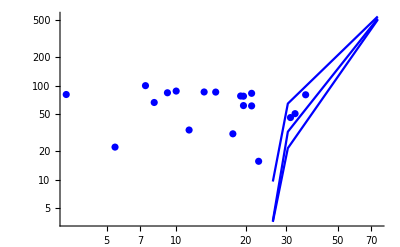

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT2DCa, dataT2DRelRate}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianD[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau2 D data.txt",Transpose[{dataT2DCa, dataT2DRelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]],simParamMedianD[[simParam,All]],simParamQuantile2D[[simParam,All]]}];
Export["plot InvTau2 D fit - quantiles and median.txt",toExport,"Table"];
];
```

### C5 and C10 and D

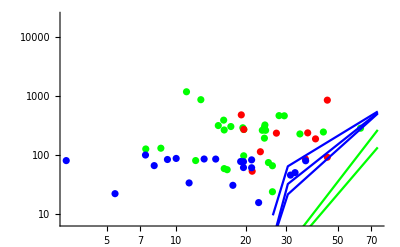

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{All,{2,10}}]
```

```mathematica
Show[gr1a,gr1b,gr1c,PlotRange->All];
```

## amp1 of bi fits (if bi is justified)

```mathematica
simParam=14;
```

### C5

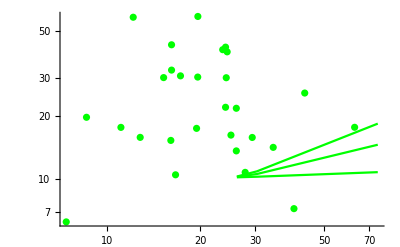

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT2C5Ca, dataT2C5Amplitude1}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{ colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
```

### C10

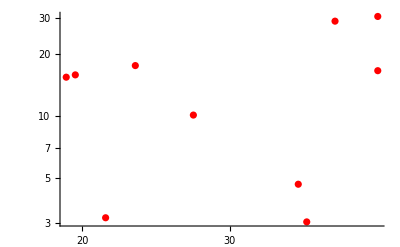

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT2C10Ca, dataT2C10Amplitude1}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
```

### D

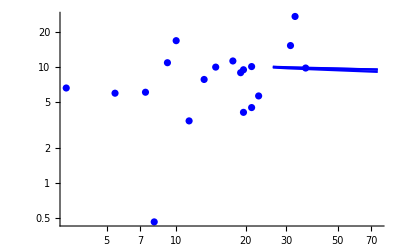

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT2DCa, dataT2DAmplitude1}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianD[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1D[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2D[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
```

### C5 and C10 and D

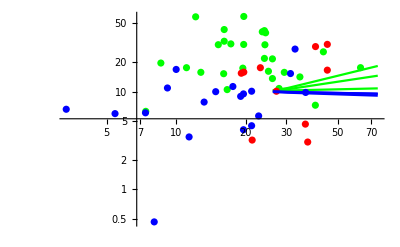

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->All]
Show[gr1a,gr1b,gr1c,PlotRange->All];
```

## chi2 mono/bi ratio

```mathematica
simParam=6;
```

### C5

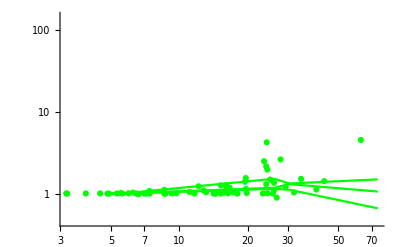

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca,dataT1C5ChiRatio}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->{All,{-0.8,5}} ]
If[exportYes==1,
Export["plot chi2Ratio C5 data.txt",Transpose[{dataT1C5Ca, dataT1C5ChiRatio}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]],simParamMedianC5[[simParam,All]],simParamQuantile2C5[[simParam,All]]}];
Export["plot chi2Ratio C5 fit - quantiles and median.txt",toExport,"Table"];
];
```

### C10

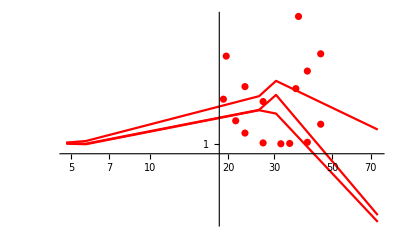

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca,dataT1C10ChiRatio}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
If[exportYes==1,
Export["plot chi2Ratio C10 data.txt",Transpose[{dataT1C10Ca, dataT1C10ChiRatio}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]],simParamMedianC10[[simParam,All]],simParamQuantile2C10[[simParam,All]]}];
Export["plot chi2Ratio C10 fit - quantiles and median.txt",toExport,"Table"];
];
```

### D

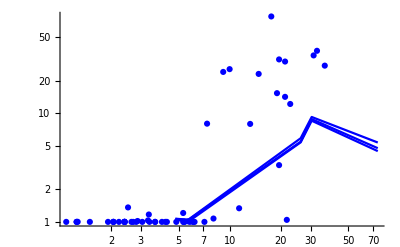

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT1DCa,dataT1DChiRatio}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianD[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2D[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
If[exportYes==1,
Export["plot chi2Ratio D data.txt",Transpose[{dataT1DCa, dataT1DChiRatio}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]],simParamMedianD[[simParam,All]],simParamQuantile2D[[simParam,All]]}];
Export["plot chi2Ratio D fit - quantiles and median.txt",toExport,"Table"];
];
```

### C5 and C10 and D

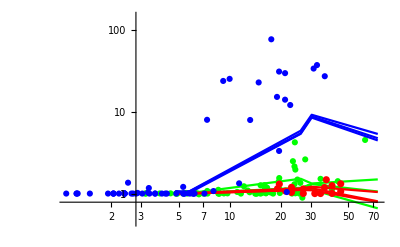

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{All,{-0.8,5}}]
Show[gr1a,gr1b,gr1c,PlotRange->All];
```

## Nv

time for Nv (ms) = 0.1

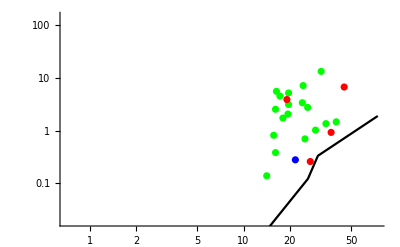

time for Nv (ms) = 0.2

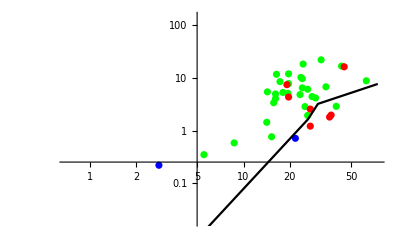

time for Nv (ms) = 1.

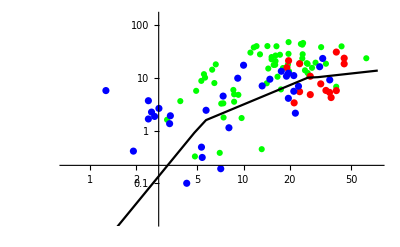

time for Nv (ms) = 5.

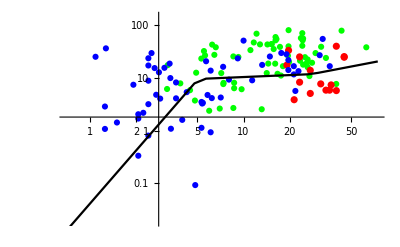

time for Nv (ms) = 10.

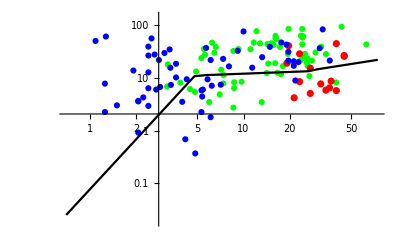

time for Nv (ms) = 100.

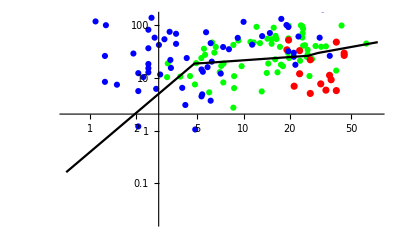

time for Nv (ms) = 400.

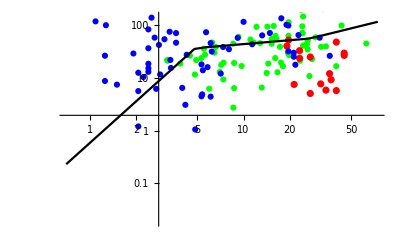

```mathematica
For[NvCount=1,NvCount≤7,NvCount+=1,
Print[" time for Nv (ms) = ",1000*timeOfNv[[NvCount]]];
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca,dataT1C5Nv[[NvCount]]}],PlotStyle->{colorA}];gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca,dataT1C10Nv[[NvCount]]}],PlotStyle->{colorB}];gr1c=ListLogLogPlot[Transpose[{dataT1DCa,dataT1DNv[[NvCount]]}],PlotStyle->{colorC}];gr2=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamNv[[NvCount,All]]}],PlotStyle ->{ Black},Joined->True, PlotRange->All];
Show[gr1a,gr1b,gr1c,gr2,PlotRange->{All,{-4,5}} ]//Print;
];
```

## sustained release 10 to 100 ms

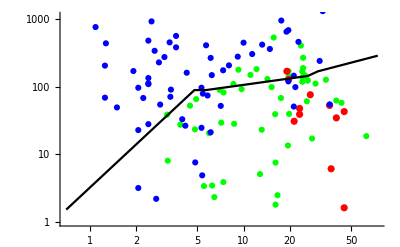

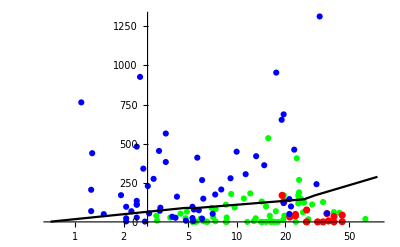

```mathematica
ttt1=Transpose[{dataT1C5Ca,(dataT1C5Nv[[6]]-dataT1C5Nv[[5]])/0.09}];
ttt2=Transpose[{dataT1C10Ca,(dataT1C10Nv[[6]]-dataT1C10Nv[[5]])/0.09}];
ttt3=Transpose[{dataT1DCa,(dataT1DNv[[6]]-dataT1DNv[[5]])/0.09}];
ttt4=Transpose[{caFact simCaList,rrp (simParamNv[[6,All]]-simParamNv[[5,All]])/0.09}];

gr1a=ListLogLogPlot[ttt1,PlotStyle->{colorA}];gr1b=ListLogLogPlot[ttt2,PlotStyle->{colorB}];gr1c=ListLogLogPlot[ttt3,PlotStyle->{colorC}];gr2=ListLogLogPlot[ttt4,PlotStyle ->{ Black},Joined->True, PlotRange->All];
Show[gr1a,gr1b,gr1c,gr2,PlotRange->{All,{0,7}} ]//Print;

gr1a=ListLogLinearPlot[ttt1,PlotStyle->{colorA}];gr1b=ListLogLinearPlot[ttt2,PlotStyle->{colorB}];gr1c=ListLogLinearPlot[ttt3,PlotStyle->{colorC}];gr2=ListLogLinearPlot[ttt4,PlotStyle ->{ Black},Joined->True, PlotRange->All];
Show[gr1a,gr1b,gr1c,gr2,PlotRange->{All,All} ]//Print;
```

```mathematica
If[exportYes==1,
Export["plot sustained release Cm5 data.txt",ttt1,"Table"];
Export["plot sustained release Cm10 data.txt",ttt2,"Table"];
Export["plot sustained release D data.txt",ttt3,"Table"];
Export["plot sustained release sim.txt",ttt4,"Table"]
];
```

## Nv normalize to the value at 5 ms

```mathematica
timeOfNv
nromPos=5;
1000*timeOfNv[[nromPos]]
```

{0.0001,0.0002,0.001,0.005,0.01,0.1,0.4}

10.

```mathematica
dataT1DNvNorm=Transpose[Transpose[dataT1DNv]/dataT1DNv[[nromPos]]];
dataT1C10NvNorm=Transpose[Transpose[dataT1C10Nv]/dataT1C10Nv[[nromPos]]];
dataT1C5NvNorm=Transpose[Transpose[dataT1C5Nv]/dataT1C5Nv[[nromPos]]];
```

```mathematica
dataT1C5NvNorm//TableForm
```

0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.102935 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.52193×10^-14 | 0.178312 | 0.0755089 | 0.0473226 | 0.0333024 | 0.340245 | 0. | 1.39164×10^-14 | 0.0601626 | 0. | 0. | 7.19133×10^-15 | 0.0241817 | 0.0440838 | 0. | 0.0191435 | 0.114433 | 0. | 0.118442 | 0. | 0.0774881 | 0. | 1.46416×10^-14 | 0.00602208 | 1.02421×10^-14 | 0.0716702 | 0.101175 | 0.115468 | 0. | 0.0110623 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.316273 | 0. | 0. | 0. | 0.0701729 | 0. | 0. | 0. | 0. | 0.0170058 | 0. | 0. | 0. | 0. | 0.12336 | 0.202992 | 0.351351 | 0.188089 | 0.237307 | 0.136209 | 0.564724 | 0. | 0.207552 | 0.139305 | 0. | 0.113553 | 0.11357 | 0.0994779 | 0.0862469 | 0.178169 | 0.0795134 | 0.294241 | 0. | 0.262297 | 0. | 0.14845 | 0. | 0.226711 | 0.0642888 | 0.161145 | 0.177142 | 0.213373 | 0.217604 | 0. | 0.115173 | 0.00975232 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.20362 | 0.265687 | 0.42823 | 0.550679 | 0.804146 | 0.862111 | 0.657036 | 0.804743 | 0.466744 | 0.922133 | 0.226521 | 0. | 0.444507 | 0.589449 | 0. | 0.15518 | 0.367819 | 0.618488 | 0.505051 | 0.547477 | 0.513227 | 0.519289 | 0.933247 | 0.917326 | 0.544754 | 0.830177 | 0.69397 | 0.653131 | 0.639806 | 0.984375 | 0.97219 | 0.730494 | 0.559303 | 0.83967 | 0.731871 | 0.503567 | 0.488021 | 0.36372 | 0.423484 | 0.416379 | 0.740654 | 0.999425 | 0.797225 | 0. | 0.539082 | 0.482694 | 0.90113 | 0.423125 | 0.696723 | 0.629088 | 0.729281 | 0.70682 | 0.127201 | 0.636613 | 0.331405 | 0.368274 | 0.077147 | 0.306211 | 0.418689 | 0.181267 | 0. | 0.232772 | 0. | 0.0592293 | 0.134595
0.719618 | 0.914034 | 0.947765 | 0.995367 | 0.999983 | 0.961307 | 0.985586 | 0.999983 | 0.986917 | 1. | 0.86321 | 0.683794 | 0.967426 | 0.977818 | 0.965586 | 0.708108 | 0.973689 | 0.956794 | 0.984176 | 0.965348 | 0.941072 | 0.896487 | 0.98101 | 0.985262 | 0.880129 | 0.936881 | 0.963176 | 0.841825 | 0.974315 | 1. | 0.98456 | 0.911675 | 0.944403 | 0.953872 | 0.942061 | 0.833228 | 0.867192 | 0.902689 | 0.841473 | 0.835146 | 0.901232 | 1. | 0.967706 | 0.743696 | 0.939188 | 0.889259 | 1. | 0.950512 | 0.90223 | 0.924817 | 0.998695 | 0.997838 | 0.731764 | 0.99577 | 0.911563 | 0.977923 | 0.537561 | 0.918451 | 0.972435 | 0.787082 | 0.953907 | 0.895019 | 0.984865 | 0.685304 | 0.707132
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1.97523 | 1.00693 | 1.44309 | 1.00001 | 1. | 1.38099 | 1.17479 | 1. | 1.00013 | 1. | 1.18393 | 1.53164 | 1.30116 | 1.30623 | 1.03968 | 1.64805 | 1.00052 | 1.01005 | 1.00022 | 1.19403 | 1.51767 | 1.2107 | 1.18462 | 1.26526 | 1.03829 | 1.68326 | 1.36675 | 1.39883 | 1.32694 | 1. | 1.27792 | 1.07205 | 1.14733 | 1.01771 | 1.65534 | 1.12419 | 1.46156 | 1.01176 | 1.0551 | 2.13029 | 1.38531 | 1. | 1.47718 | 1.70375 | 1.34613 | 1.21175 | 1. | 1.00256 | 1.57304 | 1.04225 | 1. | 1. | 1.59812 | 1.00002 | 1.00854 | 1.00034 | 2.65238 | 1.00661 | 1.04431 | 1.30233 | 1.76776 | 1.50246 | 1.00007 | 1.38717 | 1.45179
1.98885 | 1.00693 | 1.64647 | 1.00001 | 1. | 1.52805 | 1.34343 | 1. | 1.00013 | 1. | 1.24117 | 1.79443 | 2.30436 | 2.3269 | 1.17069 | 1.71471 | 1.00052 | 1.01005 | 1.00022 | 1.21138 | 1.65758 | 1.21086 | 1.25309 | 2.14948 | 1.03829 | 2.04028 | 1.52489 | 1.39982 | 1.93919 | 1. | 2.20431 | 1.07205 | 1.33654 | 1.01771 | 2.05226 | 1.12419 | 1.46722 | 1.01176 | 1.0551 | 2.29399 | 2.36374 | 1. | 2.21681 | 1.71285 | 1.66014 | 1.21186 | 1. | 1.00256 | 3.12924 | 1.04225 | 1. | 1. | 1.88985 | 1.00002 | 1.00854 | 1.00034 | 2.67307 | 1.00661 | 1.19026 | 1.37488 | 4.32694 | 3.15888 | 1.00007 | 2.14221 | 1.71564

```mathematica
simParamNv//TableForm
simParamNvNorm=Transpose[Transpose[simParamNv]/simParamNv[[nromPos]]];
simParamNvNorm//TableForm
```

1.15733×10^-8 | 0.0000223798 | 0.0000472366 | 0.0120748 | 0.0331758 | 0.189668
4.0267×10^-7 | 0.000687618 | 0.0013287 | 0.163593 | 0.322237 | 0.77187
0.0000966667 | 0.0913074 | 0.158397 | 1.01743 | 1.03842 | 1.38687
0.00123275 | 0.791128 | 0.973861 | 1.17704 | 1.2524 | 2.06825
0.00248568 | 1.08299 | 1.13647 | 1.34602 | 1.47317 | 2.21951
0.0161613 | 1.8861 | 1.93952 | 2.64701 | 2.99457 | 4.81257
0.0229784 | 3.57675 | 3.85026 | 5.60294 | 6.15268 | 11.7524

4.656×10^-6 | 0.0000206648 | 0.0000415644 | 0.00897072 | 0.02252 | 0.0854549
0.000161996 | 0.000634927 | 0.00116915 | 0.121538 | 0.218737 | 0.347767
0.0388895 | 0.0843107 | 0.139377 | 0.755884 | 0.704891 | 0.624855
0.495941 | 0.730505 | 0.856919 | 0.874458 | 0.850142 | 0.931851
1. | 1. | 1. | 1. | 1. | 1.
6.50175 | 1.74157 | 1.70662 | 1.96655 | 2.03274 | 2.16831
9.24432 | 3.30267 | 3.38792 | 4.1626 | 4.17649 | 5.29506

time for Nv (ms) = 0.1

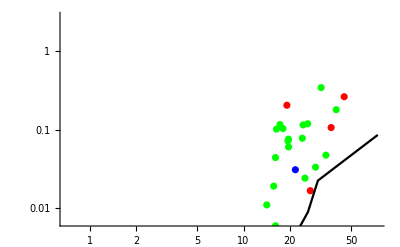

time for Nv (ms) = 0.2

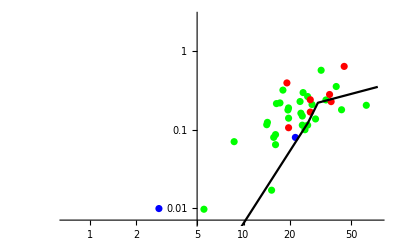

time for Nv (ms) = 1.

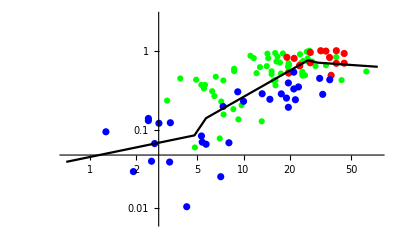

time for Nv (ms) = 5.

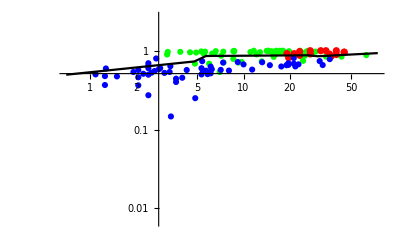

time for Nv (ms) = 10.

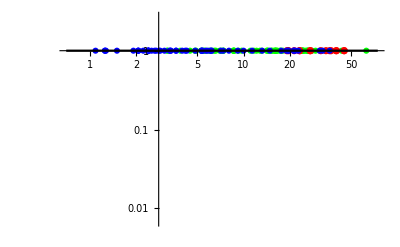

time for Nv (ms) = 100.

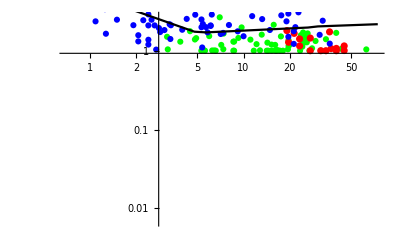

time for Nv (ms) = 400.

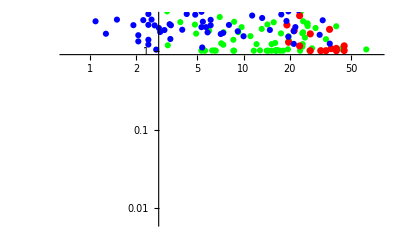

```mathematica
For[NvCount=1,NvCount≤7,NvCount+=1,
Print[" time for Nv (ms) = ",1000*timeOfNv[[NvCount]]];
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca,dataT1C5NvNorm[[NvCount]]}],PlotStyle->{colorA}];gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca,dataT1C10NvNorm[[NvCount]]}],PlotStyle->{colorB}];gr1c=ListLogLogPlot[Transpose[{dataT1DCa,dataT1DNvNorm[[NvCount]]}],PlotStyle->{colorC}];gr2=ListLogLogPlot[Transpose[{caFact simCaList, simParamNvNorm[[NvCount,All]]}],PlotStyle ->{ Black},Joined->True, PlotRange->All];
Show[gr1a,gr1b,gr1c,gr2,PlotRange->{All,{-5,1}} ]//Print;
];
```

## Export Nv

```mathematica
If[exportYes==1,
Export["Nv export Ca,0.0001,0.0002,0.001,0.005,0.01,0.1,0.4.txt",Transpose[Prepend[simParamNv,caFact simCaList]],"Table"];
];
```

## Print some values

### C5

```mathematica
Transpose[simParamMedianC5]//TableForm
Transpose[simParamQuantile1C5]//TableForm
Transpose[simParamQuantile2C5]//TableForm
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 2.5573 | 0.0015475 | 1.08303 | 325.139 | 1.00194 | 0.001514 | 0.918481 | 3.42274 | 434.887 | 82.1558 | 0.0015475 | 1.08303 | Median[{}] | 325.139 | Median[{}]
0 | 2.50461 | 0.000567899 | 1.16243 | 370.508 | 1.0028 | 0.000574885 | 2.43724 | 1.17015 | 351.293 | 3.78394 | 0.000567899 | 1.16243 | Median[{}] | 370.508 | Median[{}]
0 | 2.59839 | 0.000363778 | 1.22787 | 6471.19 | 1.17733 | 0.00032778 | 19.7921 | 1.02137 | 12943.1 | 3.23028 | 0.000149017 | 11.3848 | 1.02572 | 3678.12 | 2.68576
0 | 3.2711 | 0.000180307 | 1.26031 | 5693.99 | 1.30575 | 0.000386272 | 20.6257 | 1.02791 | 142096. | 1.67923 | 0.000384815 | 19.3501 | 1.0591 | 118018. | 2.23635
0 | 3.27193 | -0.000267639 | 2.13923 | 804.964 | 1.05917 | 4.60679×10^-6 | 2.32967 | 1.23373 | 149478. | 265.732 | -0.000183647 | 2.32967 | 1.45589 | 1189.06 | 134.505

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 2.51606 | 0.000713634 | 0.971947 | 255.849 | 1.00121 | 0.001 | 0.588799 | 0.753421 | 156.775 | 19.0183 | 0.000713634 | 0.971947 | Quantile[{},0.25] | 255.849 | Quantile[{},0.25]
0 | 2.47782 | 0.000290398 | 1.1077 | 336.311 | 1.00004 | 0.000370448 | 0.962649 | 0.829175 | 232.14 | 2.45632 | 0.000290398 | 1.1077 | Quantile[{},0.25] | 336.311 | Quantile[{},0.25]
0 | 2.49861 | -0.0004 | 1.17334 | 565.925 | 1.14234 | 0.000149017 | 11.3848 | 0.8795 | 3678.12 | 1.56096 | -0.0004 | 1.33533 | 1.02137 | 565.925 | 1.56096
0 | 2.85294 | 9.32334×10^-17 | 1.25169 | 1377. | 1.11441 | 0.000384815 | 19.3501 | 1.01907 | 118018. | 1.63278 | 0.000180307 | 1.26031 | 1.02791 | 6190.3 | 1.63278
0 | 2.85416 | -0.000380157 | 2.10942 | 621.78 | 0.659316 | -0.000183647 | 2.20229 | 1.08023 | 1189.06 | 3.27711 | -0.000255979 | 2.1793 | 1.08023 | 804.964 | 3.27711

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 2.96309 | 0.00170589 | 1.33129 | 665.904 | 1.00705 | 0.00168772 | 2.66801 | 3.71225 | 562.932 | 359.175 | 0.00170589 | 1.33129 | Quantile[{},0.75] | 665.904 | Quantile[{},0.75]
0 | 2.75443 | 0.000696149 | 1.21975 | 389.051 | 1.0049 | 0.000663083 | 13.0031 | 5.53286 | 544.202 | 189.202 | 0.000696149 | 1.21975 | Quantile[{},0.75] | 389.051 | Quantile[{},0.75]
0 | 2.70432 | 0.000399859 | 1.33533 | 3.93924×10^6 | 1.51932 | 0.000394608 | 21.0452 | 1.03006 | 122865. | 3.81055 | 0.000394608 | 19.7921 | 1.03006 | 122865. | 3.81055
0 | 3.43923 | 0.000198141 | 1.33147 | 6190.3 | 1.32917 | 0.000394903 | 29.9872 | 1.0903 | 6.51487×10^6 | 2.83993 | 0.000386272 | 20.6257 | 1.0903 | 142096. | 2.83993
0 | 3.78636 | -0.000255979 | 2.1793 | 831.044 | 1.49132 | 0.000588848 | 13.6711 | 1.83156 | 256665. | 614.554 | 4.60679×10^-6 | 13.6711 | 1.83156 | 256665. | 265.732

### C10

```mathematica
Transpose[simParamMedianC10]//TableForm
Transpose[simParamQuantile1C10]//TableForm
Transpose[simParamQuantile2C10]//TableForm
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 7.67019 | 0.0002 | 1.20006 | 210.934 | 1.00267 | 0.0002 | 1.86025 | 1.68345 | 196.646 | 80.8203 | 0.0002 | 1.20006 | Median[{}] | 210.934 | Median[{}]
0 | 7.83462 | 0.000660373 | 1.17692 | 387.588 | 1.00005 | 0.000672742 | 1.33513 | 1.05089 | 473.462 | 16.7979 | 0.000660373 | 1.17692 | Median[{}] | 387.588 | Median[{}]
0 | 8.86808 | -0.0001 | 1.23306 | 1219.14 | 1.10937 | 0.0002 | 12.0535 | 0.957703 | 5352.85 | 3.87246 | 0.0002 | 12.0535 | 0.957703 | 5352.85 | 3.87246
0 | 8.52541 | 1.62524×10^-16 | 1.29638 | 2129.89 | 1.16152 | 0.000077443 | 21.7689 | 1.03527 | 5391.05 | 2.12433 | 1.62524×10^-16 | 1.29638 | Median[{}] | 2129.89 | Median[{}]
0 | 8.25029 | -0.000296348 | 2.12344 | 719.972 | 0.803446 | 0.00048757 | 2.15823 | 1.08242 | 297842. | 558.61 | -0.0002 | 2.13033 | 1.38028 | 759.926 | 295.322

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 7.13307 | 0.0002 | 1.01403 | 94.1928 | 1. | 0.0002 | 0.537452 | 0.669868 | 95.0762 | 44.7008 | 0.0002 | 1.01403 | Quantile[{},0.25] | 94.1928 | Quantile[{},0.25]
0 | 7.7142 | 0.0005 | 1.08961 | 359.436 | 0.998535 | 0.0005 | 1.3105 | 0.76409 | 398.63 | 3.3025 | 0.0005 | 1.08961 | Quantile[{},0.25] | 359.436 | Quantile[{},0.25]
0 | 6.98349 | -0.000133562 | 1.22277 | 1021.09 | 1.10818 | 0.000183393 | 1.47482 | 0.920761 | 3273.71 | 2.41423 | 0.000183393 | 1.47482 | 0.920761 | 3273.71 | 2.41423
0 | 7.78874 | -0.0000334745 | 1.22767 | 1503.9 | 1.09687 | 0.0000409327 | 21.2499 | 0.977916 | 3170.08 | 1.28762 | -0.0000334745 | 1.22767 | Quantile[{},0.25] | 1503.9 | Quantile[{},0.25]
0 | 6.56636 | -0.000358176 | 2.09501 | 703.854 | 0.786879 | 0.000048708 | 2.12862 | 1.01187 | 2331.64 | 295.322 | -0.000296348 | 2.09501 | 1.38028 | 719.972 | 295.322

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 9.18484 | 0.000718121 | 1.89261 | 296.268 | 1.00335 | 0.0007 | 1.889 | 2.0822 | 324.465 | 89.3533 | 0.000718121 | 1.89261 | Quantile[{},0.75] | 296.268 | Quantile[{},0.75]
0 | 8.54551 | 0.001 | 1.26908 | 455.74 | 1.00837 | 0.00107778 | 15.6713 | 1.08952 | 692.258 | 149.571 | 0.001 | 1.26908 | Quantile[{},0.75] | 455.74 | Quantile[{},0.75]
0 | 10.2785 | 0.0002 | 1.24519 | 2142.35 | 1.15701 | 0.000298236 | 19.0487 | 0.988569 | 216129. | 152.216 | 0.000298236 | 19.0487 | 0.988569 | 216129. | 152.216
0 | 10.5612 | 0.0001 | 1.30379 | 3170.57 | 1.21262 | 0.000163589 | 36.004 | 1.04776 | 9086.9 | 2.30306 | 0.0001 | 1.30379 | Quantile[{},0.75] | 3170.57 | Quantile[{},0.75]
0 | 10.0302 | -0.0002 | 2.13033 | 759.926 | 1.04435 | 0.000497848 | 2.22656 | 1.38028 | 416456. | 568.115 | 0.000048708 | 2.22656 | 1.38028 | 2331.64 | 295.322

### D

```mathematica
Transpose[simParamMedianD]//TableForm
Transpose[simParamQuantile1D]//TableForm
Transpose[simParamQuantile2D]//TableForm
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0.182211 | 0.000756457 | 1.23782 | 233.591 | 1.06421 | 0.000729688 | 0.497869 | 3.25809 | 146.347 | 68.8509 | 0.000756457 | 1.23782 | Median[{}] | 233.591 | Median[{}]
0 | 0.161382 | 0.000643901 | 1.14624 | 422.665 | 1.04016 | 0.000581982 | 0.957308 | 3.21524 | 261.369 | 173.873 | 0.000643901 | 1.14624 | Median[{}] | 422.665 | Median[{}]
0 | 0.801939 | 0.0000430933 | 1.21328 | 1803.62 | 5.47494 | 0.00016417 | 10.9096 | 1.00337 | 4483.18 | 3.64017 | 0.00016417 | 10.9096 | 1.00337 | 4483.18 | 3.64017
0 | 1.30632 | -0.000152542 | 1.31013 | 1131.46 | 8.83763 | 0.000148537 | 2.78601 | 0.988914 | 7797.13 | 32.3135 | 0.000148537 | 2.78601 | 0.988914 | 7797.13 | 32.3135
0 | 0.883126 | -0.000194146 | 2.12802 | 845.567 | 4.76792 | 0.0000807884 | 2.18304 | 0.952218 | 11318.1 | 517.071 | 0.0000807884 | 2.18304 | 0.952218 | 11318.1 | 517.071

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0.175917 | 0.00071855 | 1.23443 | 227.397 | 1.04785 | 0.000679706 | 0.47317 | 3.07318 | 139.657 | 66.8991 | 0.00071855 | 1.23443 | Quantile[{},0.25] | 227.397 | Quantile[{},0.25]
0 | 0.148427 | 0.000526628 | 1.1405 | 377.03 | 1.00324 | 0.000473957 | 0.757604 | 1.19383 | 236.871 | 14.3652 | 0.000526628 | 1.1405 | Quantile[{},0.25] | 377.03 | Quantile[{},0.25]
0 | 0.78905 | -3.23016×10^-16 | 1.2127 | 1577.97 | 5.39822 | 0.000153394 | 4.99995 | 0.991888 | 4393.12 | 3.55115 | 0.000153394 | 4.99995 | 0.991888 | 4393.12 | 3.55115
0 | 1.30204 | -0.000188535 | 1.302 | 1064.45 | 8.53879 | 0.000142348 | 2.00784 | 0.975877 | 6633.52 | 21.602 | 0.000142348 | 2.00784 | 0.975877 | 6633.52 | 21.602
0 | 0.803753 | -0.000210221 | 2.12229 | 829.381 | 4.48386 | 0.0000795971 | 2.16914 | 0.909639 | 10245.9 | 502.436 | 0.0000795971 | 2.16914 | 0.909639 | 10245.9 | 502.436

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0.192411 | 0.000844248 | 1.2548 | 242.66 | 1.07016 | 0.000816872 | 0.531413 | 3.3216 | 146.761 | 71.5422 | 0.000844248 | 1.2548 | Quantile[{},0.75] | 242.66 | Quantile[{},0.75]
0 | 0.161997 | 0.000787771 | 1.18599 | 464.712 | 1.04593 | 0.000777558 | 1.00402 | 3.76291 | 439.599 | 178.216 | 0.000787771 | 1.18599 | Quantile[{},0.75] | 464.712 | Quantile[{},0.75]
0 | 0.817046 | 0.0000776317 | 1.21352 | 1882.15 | 5.88857 | 0.000170968 | 11.3394 | 1.00602 | 4522.44 | 9.54676 | 0.000170968 | 11.3394 | 1.00602 | 4522.44 | 9.54676
0 | 1.39955 | -0.000105043 | 1.31664 | 1260.85 | 9.24529 | 0.000149554 | 3.4867 | 0.996275 | 7890.25 | 64.3718 | 0.000149554 | 3.4867 | 0.996275 | 7890.25 | 64.3718
0 | 0.917844 | -0.000192623 | 2.12918 | 854.09 | 5.37949 | 0.0000918707 | 2.18666 | 0.952357 | 16414. | 543.74 | 0.0000918707 | 2.18666 | 0.952357 | 16414. | 543.74

### Nv

```mathematica
Transpose[simParamNv]//TableForm
```

1.15733×10^-8 | 4.0267×10^-7 | 0.0000966667 | 0.00123275 | 0.00248568 | 0.0161613 | 0.0229784
0.0000223798 | 0.000687618 | 0.0913074 | 0.791128 | 1.08299 | 1.8861 | 3.57675
0.0000472366 | 0.0013287 | 0.158397 | 0.973861 | 1.13647 | 1.93952 | 3.85026
0.0120748 | 0.163593 | 1.01743 | 1.17704 | 1.34602 | 2.64701 | 5.60294
0.0331758 | 0.322237 | 1.03842 | 1.2524 | 1.47317 | 2.99457 | 6.15268
0.189668 | 0.77187 | 1.38687 | 2.06825 | 2.21951 | 4.81257 | 11.7524

# EPSC with different caRest

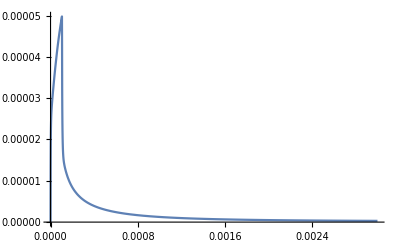

```mathematica
locaCa=Transpose[{dataLocalCaTime,dataLocalCa}];
locaCaWithoutdublictes=Mean/@GatherBy[locaCa,First];
interpolFunc=Interpolation[locaCaWithoutdublictes,InterpolationOrder->1];
caFunc[t_]:=interpolFunc[t];
Plot[caFunc[t],{t,0.00,0.003},PlotRange->All]
```

## NDSolve

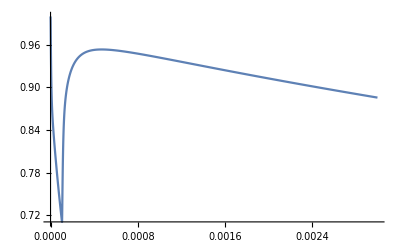

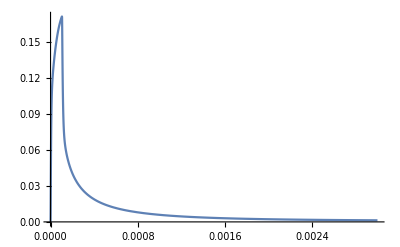

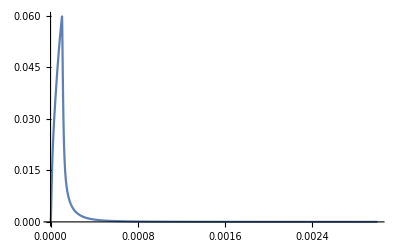

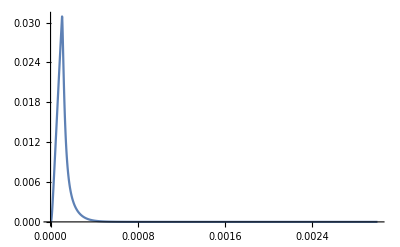

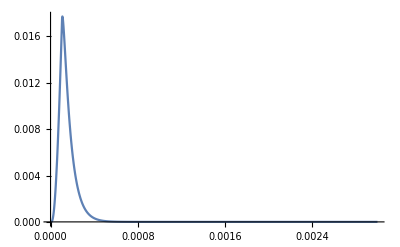

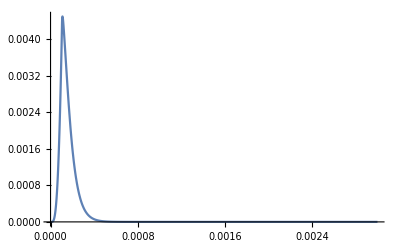

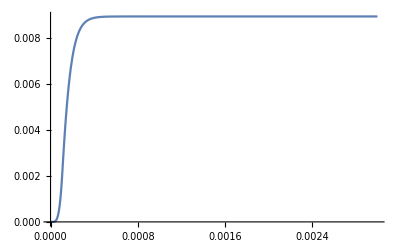

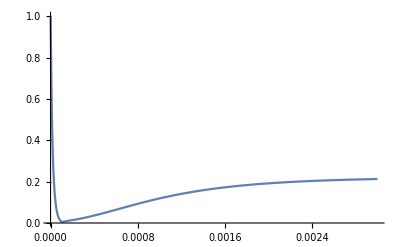

```mathematica
timeStartForPLot=0.0;
timeEndForPLot=0.003;
myNDSolveResults=NDSolve[eq,{ss1A,ss2A,ss3A,ss4A,ss5A,ss6A,ss7A,ss1B,ss2B,ss3B,ss4B,ss5B,ss6B,ss7B},{t,0,0.003}];
Plot[(ss1A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss2A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss3A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss4A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss5A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss6A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss7A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss1B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss2B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss3B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss4B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss5B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss6B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss7B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
```

## different caRest

```mathematica
caRestLow=30*^-9;
caRestHigh=180*^-9;
```

## Low Ca

## Initial occupancy

```mathematica
(*calualte initial equilibrium occupancy*)
caFunc[t_]:=caRestLow;
ss0AInitial=kprimSchemeA/kunprimSchemeA
ss0BInitial=(kprimSchemeA/kunprimSchemeA)*(kprimSchemeB/kunprimSchemeB)
```

1.

0.26514

## Diff eq.

```mathematica
Clear[caFunc,eq];(*Clear is needed if the cell is exectued for a 2nd time when caFunc is already set to a value or an Interpolationfunction*)
caFunc[t_]:=interpolFunc[t];
ssA[t_]={ss1A[t],ss2A[t],ss3A[t],ss4A[t],ss5A[t],ss6A[t],ss7A[t]};
ssB[t_]={ss1B[t],ss2B[t],ss3B[t],ss4B[t],ss5B[t],ss6B[t],ss7B[t]};
eq={
ssA'[t]==(matA/.repl).ssA[t],
ssA[0]=={ss0AInitial,0,0,0,0,0,0},

ssB'[t]==(matB/.repl).ssB[t],
ssB[0]=={ss0BInitial,0,0,0,0,0,0}
};
```

## NDSolve

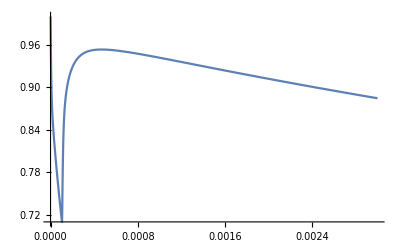

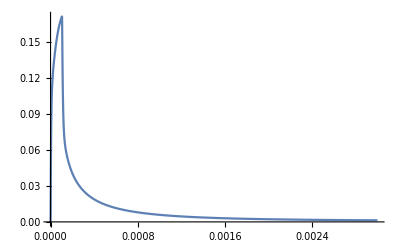

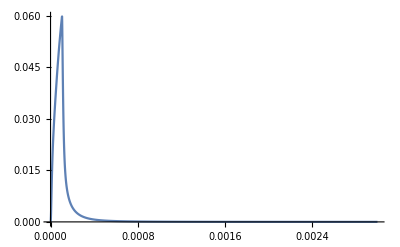

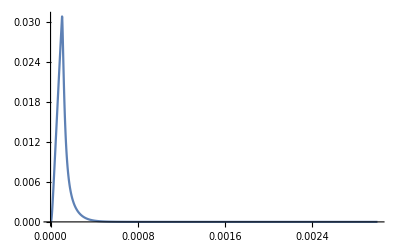

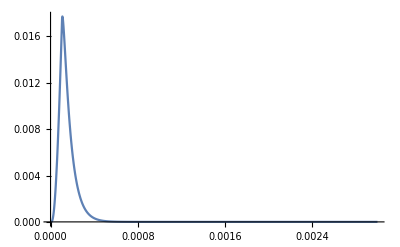

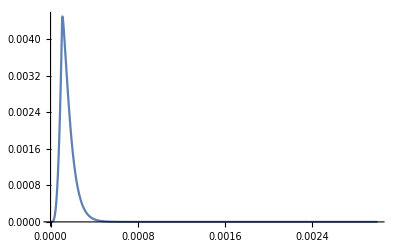

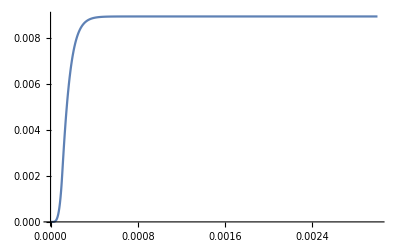

------------------------------------------------------------------

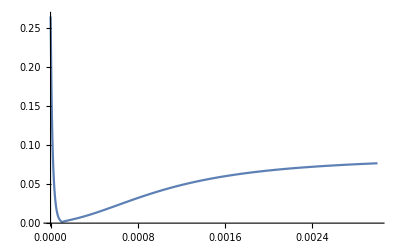

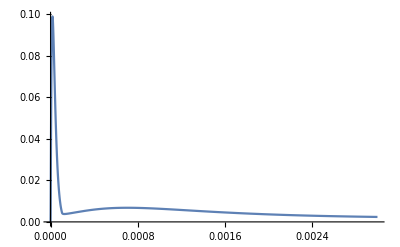

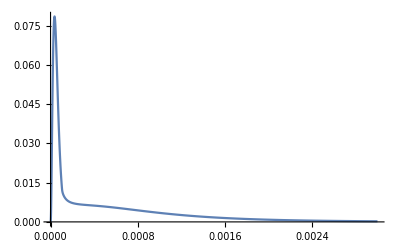

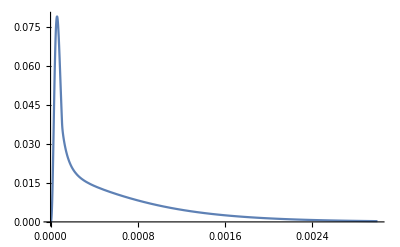

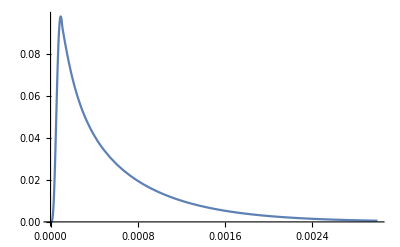

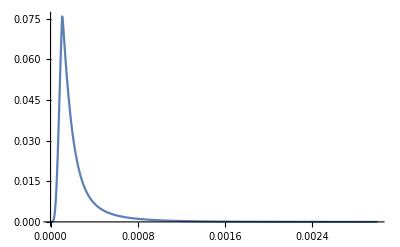

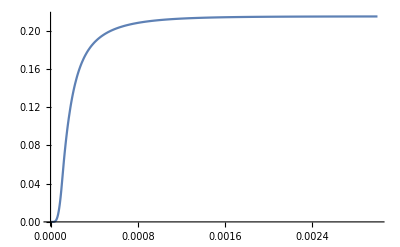

```mathematica
myNDSolveResults=NDSolve[eq,{ss1A,ss2A,ss3A,ss4A,ss5A,ss6A,ss7A,ss1B,ss2B,ss3B,ss4B,ss5B,ss6B,ss7B},{t,0,0.003}];
Plot[(ss1A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss2A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss3A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss4A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss5A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss6A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss7A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Print["------------------------------------------------------------------"];
Plot[(ss1B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss2B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss3B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss4B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss5B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss6B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss7B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
```

## Plot EPSC

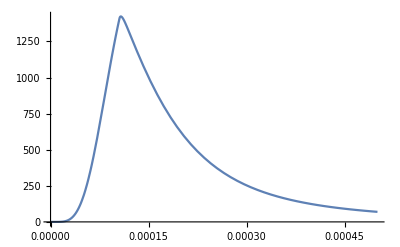

```mathematica
epscLowCa=D[((ss7A[t]+ss7B[t])/.myNDSolveResults),t];
Plot[epscLowCa,{t,0,2.*^-3},PlotRange->All];
Plot[epscLowCa,{t,0,0.5*^-3},PlotRange->All]
```

## High Ca

## Initial occupancy

```mathematica
(*calualte initial equilibrium occupancy*)
caFunc[t_]:=caRestHigh;
ss0AInitial=kprimSchemeA/kunprimSchemeA
ss0BInitial=(kprimSchemeA/kunprimSchemeA)*(kprimSchemeB/kunprimSchemeB)
```

1.

0.836742

## Diff eq.

```mathematica
Clear[caFunc,eq];(*Clear is needed if the cell is exectued for a 2nd time when caFunc is already set to a value or an Interpolationfunction*)
caFunc[t_]:=interpolFunc[t];
ssA[t_]={ss1A[t],ss2A[t],ss3A[t],ss4A[t],ss5A[t],ss6A[t],ss7A[t]};
ssB[t_]={ss1B[t],ss2B[t],ss3B[t],ss4B[t],ss5B[t],ss6B[t],ss7B[t]};
eq={
ssA'[t]==(matA/.repl).ssA[t],
ssA[0]=={ss0AInitial,0,0,0,0,0,0},

ssB'[t]==(matB/.repl).ssB[t],
ssB[0]=={ss0BInitial,0,0,0,0,0,0}
};
```

## NDSolve

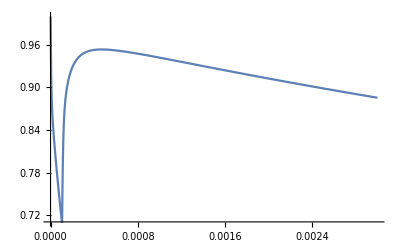

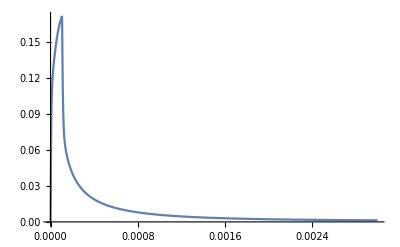

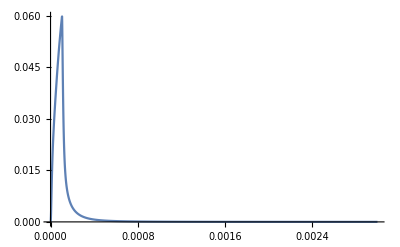

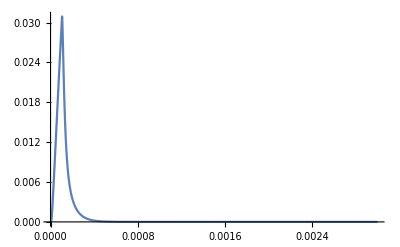

-Graphics-

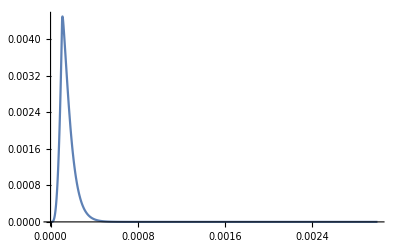

-Graphics-

------------------------------------------------------------------

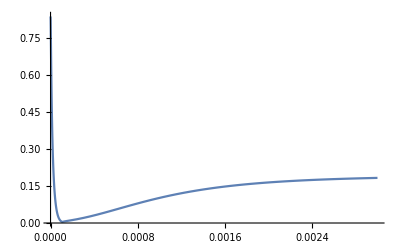

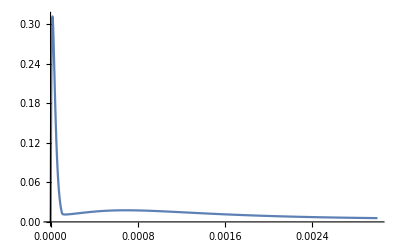

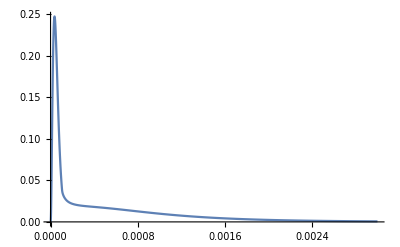

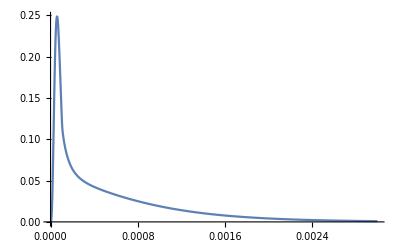

-Graphics-

-Graphics-

-Graphics-

```mathematica
myNDSolveResults=NDSolve[eq,{ss1A,ss2A,ss3A,ss4A,ss5A,ss6A,ss7A,ss1B,ss2B,ss3B,ss4B,ss5B,ss6B,ss7B},{t,0,0.003}];
Plot[(ss1A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss2A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss3A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss4A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss5A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss6A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss7A[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Print["------------------------------------------------------------------"];
Plot[(ss1B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss2B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss3B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss4B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss5B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss6B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss7B[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
```

## Plot EPSC

```mathematica
epscHighCa=D[((ss7A[t]+ss7B[t])/.myNDSolveResults),t];
Plot[epscHighCa,{t,0,2*^-3},PlotRange->All];
Plot[epscHighCa,{t,0,0.5*^-3},PlotRange->All]
```

-Graphics-

## Compare

## Plot both release rates

```mathematica
Plot[{epscLowCa,epscHighCa},{t,0,0.5*^-3},PlotRange->All]
```

-Graphics-

## Convolution RelRate => EPSC

```mathematica
miniKernel[t_]:=If[t≤0,0,(1-Exp[-t/0.0001])*Exp[-t/0.002]];
Plot[miniKernel[t],{t,-.001,.01}]
dtForConvolve=0.00005;
tEndConv=0.01;
miniKernelList=Table[miniKernel[t],{t,0.0,tEndConv,dtForConvolve}];
epscHighCaList={Table[0,{t,0,tEndConv,dtForConvolve}],Table[epscHighCa,{t,0.0,0.0025,dtForConvolve}],Table[0,{t,0,tEndConv,dtForConvolve}]}//Flatten;epscLowCaList={Table[0,{t,0,tEndConv,dtForConvolve}],Table[epscLowCa,{t,0.0,0.0025,dtForConvolve}],Table[0,{t,0,tEndConv,dtForConvolve}]}//Flatten;
ListPlot[miniKernelList]
ListPlot[epscLowCaList,PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
epscLowCaCurrentList=ListConvolve[miniKernelList,epscLowCaList];
epscHighCaCurrentList=ListConvolve[miniKernelList,epscHighCaList];
timeConv=Table[t*dtForConvolve,{t,Length[epscLowCaCurrentList]}];
ListPlot[{Transpose[{timeConv,epscLowCaCurrentList}],Transpose[{timeConv,epscHighCaCurrentList}]},Joined->True,PlotRange->All]
ListPlot[{Transpose[{timeConv,epscLowCaCurrentList}],Transpose[{timeConv,epscHighCaCurrentList}]},Joined->True,PlotRange->{{0,0.002},All}]
maxLow=Max[epscLowCaCurrentList]
maxHigh=Max[epscHighCaCurrentList]
Print["maxHigh/maxLow = ",maxHigh/maxLow];
ListPlot[{Transpose[{timeConv,(1/maxLow)*epscLowCaCurrentList}],Transpose[{timeConv,(1/maxHigh)*epscHighCaCurrentList}]},Joined->True,PlotRange->All]
ListPlot[{Transpose[{timeConv,(1/maxLow)*epscLowCaCurrentList}],Transpose[{timeConv,(1/maxHigh)*epscHighCaCurrentList}]},Joined->True,PlotRange->{{0,0.002},All}]
If[exportYes==1,
toExport=Transpose[{timeConv,epscLowCaCurrentList,epscHighCaCurrentList,(1/maxLow)*epscLowCaCurrentList,(1/maxHigh)*epscHighCaCurrentList}];
Export["plot EPSC - low and high - abs and norm.txt",toExport,"Table"];
];
```

-Graphics-

-Graphics-

3304.39

10076.8

maxHigh/maxLow = 3.0495

-Graphics-

-Graphics-

# Timing

```mathematica
timeEnd=AbsoluteTime[]
(timeEnd-timeStart )/60.(*time of calculation in min*)
```

3.841510563799333×10^9

0.313377